## Initializing

```mathematica
resfinal={{4.404296875,5.38037109375},{8.30859375,9.28466796875},{14.1650390625,15.14111328125},{21.9736328125,22.94970703125},{30.75830078125,31.734375},{41.4951171875,42.47119140625},{53.2080078125,54.18408203125},{66.873046875,67.84912109375},{82.490234375,83.46630859375},{99.08349609375,100.0595703125},{116.65283203125,117.62890625},{137.150390625,138.12646484375},{158.6240234375,159.60009765625},{181.07373046875,182.0498046875},{206.45166015625,207.427734375},{231.82958984375,232.8056640625},{260.1357421875,261.11181640625},{289.41796875,290.39404296875},{320.65234375,321.62841796875},{352.86279296875,353.8388671875},{387.025390625,388.00146484375},{422.1640625,423.14013671875},{459.2548828125,460.23095703125},{498.2978515625,499.27392578125},{538.31689453125,539.29296875},{580.2880859375,581.26416015625},{623.2353515625,624.21142578125},{669.11083984375,670.0869140625},{714.986328125,715.96240234375},{763.7900390625,764.76611328125},{812.59375,813.56982421875},{864.32568359375,865.3017578125},{917.03369140625,918.009765625},{971.69384765625,972.669921875}};
```

Above is from emcmanis_findcriticalvalues.nb. Run with rho_inf = 20*λ.

```mathematica
Critical[λ_,consts_]:=Module[{H,res,dρ,ρinf,nn},
dρ=consts[[1]];
ρinf=Round[consts[[2]]];
nn=Round[ρinf/dρ];
(*Print["dρ = "<>ToString[dρ]<>", ρinf = "<>ToString[ρinf]<>", and nn = "<>ToString[nn]<>"."];*)
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ)+(2(*=l(l+1)*))/(n*dρ)^2,{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-25]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

```mathematica
CountNegs[list_]:=Module[{neg,i},
neg=0;
For[i=1,list[[i]]<0,i++,
neg++;
];
Return[neg]
]
```

```mathematica
Bisect[F_,consts_,x0_,xf_,ϵ_]:=Module[{mid,val,lnegs,vam,mnegs,vah},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint is "<>ToString[mid]];
val=F[x0,consts];
lnegs=CountNegs[val];
vam=F[mid,consts];
mnegs=CountNegs[vam];
If[xf-x0>ϵ,
(*Print[{lnegs,mnegs},{val[[1]],vam[[1]]}];*)
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]), (*if there is a zero on the lower half*)
Return[Bisect[F,consts,x0,mid,ϵ]];, (*bisect it*)
Return[Bisect[F,consts,mid,xf,ϵ]]; (*otherwise try the upper half*)
];,
vah = F[xf,consts];
Return[{mid,lnegs,CountNegs[vah]}];
]
]
```

```mathematica
rhoinfs={40,80};
```

### Junk?

```mathematica
ParallelTable[{i,j,Evaluate[$KernelID],Timing[Bisect[Critical,{0.01,rhoinfs[[j]],rhoinfs[[j]]/0.01},resfinal[[i,1]],resfinal[[i,2]],10.^(-6)]]},{i,1,2},{j,1,3}]
```

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 20.1514

```mathematica
Parallelize[Table[i,{i,1,10}]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
lcs=Parallelize[Table[Table[{j,Bisect[Critical,{0.01,rhoinfs[[j]],rhoinfs[[j]]/0.01},resfinal[[i,1]],resfinal[[i,2]],10^(-6)]},{j,1,3}],{i,1,Length[resfinal]}]];
```

```mathematica
ParallelTable[i+2,{i,1,10}]
```

{3,4,5,6,7,8,9,10,11,12}

## The Actual Computation

### Computing (TAKES A LONG TIME DO NOT EVALUATE)

{tag, rhoinf, lambda1, lambda2} = > {tag, lc[rhoinf]} <- format of this function below me. This opaque mess massages the data into something easily parallelized. This is the setup for refining the functions. We will do a refinement at each value of rhoinf.

```mathematica
inputs=Table[Table[{j,rhoinfs[[j]]*resfinal[[i,1]],resfinal[[i,1]]-2,resfinal[[i,2]]+2},{j,1,1}],{i,1,Floor[Length[resfinal]]}]
```

{{{1,176.172,2.4043,7.38037}},{{1,332.344,6.30859,11.2847}},{{1,566.602,12.165,17.1411}},{{1,878.945,19.9736,24.9497}},{{1,1230.33,28.7583,33.7344}},{{1,1659.8,39.4951,44.4712}},{{1,2128.32,51.208,56.1841}},{{1,2674.92,64.873,69.8491}},{{1,3299.61,80.4902,85.4663}},{{1,3963.34,97.0835,102.06}},{{1,4666.11,114.653,119.629}},{{1,5486.02,135.15,140.126}},{{1,6344.96,156.624,161.6}},{{1,7242.95,179.074,184.05}},{{1,8258.07,204.452,209.428}},{{1,9273.18,229.83,234.806}},{{1,10405.4,258.136,263.112}},{{1,11576.7,287.418,292.394}},{{1,12826.1,318.652,323.628}},{{1,14114.5,350.863,355.839}},{{1,15481.,385.025,390.001}},{{1,16886.6,420.164,425.14}},{{1,18370.2,457.255,462.231}},{{1,19931.9,496.298,501.274}},{{1,21532.7,536.317,541.293}},{{1,23211.5,578.288,583.264}},{{1,24929.4,621.235,626.211}},{{1,26764.4,667.111,672.087}},{{1,28599.5,712.986,717.962}},{{1,30551.6,761.79,766.766}},{{1,32503.8,810.594,815.57}},{{1,34573.,862.326,867.302}},{{1,36681.3,915.034,920.01}},{{1,38867.8,969.694,974.67}}}

```mathematica
inputs=Flatten[inputs,1]
```

{{1,176.172,2.4043,7.38037},{1,332.344,6.30859,11.2847},{1,566.602,12.165,17.1411},{1,878.945,19.9736,24.9497},{1,1230.33,28.7583,33.7344},{1,1659.8,39.4951,44.4712},{1,2128.32,51.208,56.1841},{1,2674.92,64.873,69.8491},{1,3299.61,80.4902,85.4663},{1,3963.34,97.0835,102.06},{1,4666.11,114.653,119.629},{1,5486.02,135.15,140.126},{1,6344.96,156.624,161.6},{1,7242.95,179.074,184.05},{1,8258.07,204.452,209.428},{1,9273.18,229.83,234.806},{1,10405.4,258.136,263.112},{1,11576.7,287.418,292.394},{1,12826.1,318.652,323.628},{1,14114.5,350.863,355.839},{1,15481.,385.025,390.001},{1,16886.6,420.164,425.14},{1,18370.2,457.255,462.231},{1,19931.9,496.298,501.274},{1,21532.7,536.317,541.293},{1,23211.5,578.288,583.264},{1,24929.4,621.235,626.211},{1,26764.4,667.111,672.087},{1,28599.5,712.986,717.962},{1,30551.6,761.79,766.766},{1,32503.8,810.594,815.57},{1,34573.,862.326,867.302},{1,36681.3,915.034,920.01},{1,38867.8,969.694,974.67}}

```mathematica
inputs[[1]]
```

{1,176.172,2.4043,7.38037}

```mathematica
Findlc[input_,i_,eps_]:=Module[{val,vah,lnegs,hnegs,res},
Print["***Beginning to calculate the "<>ToString[Ceiling[i,2]/2]<>"th lambda, part "<>ToString[input[[1]]]];
val=Critical[input[[3]],{0.1,input[[2]],input[[2]]/0.1}];
vah=Critical[input[[4]],{0.1,input[[2]],input[[2]]/0.1}];
lnegs=CountNegs[val];
hnegs=CountNegs[vah];
If[lnegs<hnegs || (lnegs==hnegs && val[[1]]<vah[[1]]),(*doublechecks for zero*)
Print["Pass!"];
res={input[[1]],Bisect[Critical,{0.1,input[[2]],input[[2]]/0.1},input[[3]],input[[4]],eps]};
,(*else*)
Print["Fail!"];
res={input[[1]],Null};
];
Return[res]
]
```

```mathematica
DistributeDefinitions[Findlc,Bisect,Critical,CountNegs,inputs]
```

```mathematica
Critical[inputs[[1,3]],{0.1,inputs[[1,2]],inputs[[1,2]]/0.1}]
```

{0.000650777,0.00192193,0.0038244,0.00635422,0.00950662,0.0132767,0.01766,0.0226533,0.0282546,0.0344639,0.0412829,0.0487148,0.0567635,0.0654337,0.0747298,0.0846556,0.0952145,0.106409,0.118241,0.130712,0.143823,0.157574,0.171966,0.186998,0.202672}

#### Refinement Process

```mathematica
refinement=ParallelTable[Findlc[inputs[[i]],i,0.25],{i,1,Length[inputs]}]
```

***Beginning to calculate the 1th lambda, part 1

***Beginning to calculate the 2th lambda, part 1

***Beginning to calculate the 4th lambda, part 1

***Beginning to calculate the 5th lambda, part 1

***Beginning to calculate the 7th lambda, part 1

Pass!

Bisecting. Midpoint is 4.89233

Bisecting. Midpoint is 3.64832

Bisecting. Midpoint is 4.27032

Bisecting. Midpoint is 4.58133

Bisecting. Midpoint is 4.42583

Bisecting. Midpoint is 4.50358

Pass!

Bisecting. Midpoint is 22.4617

***Beginning to calculate the 1th lambda, part 1

Pass!

Bisecting. Midpoint is 8.79663

Bisecting. Midpoint is 10.0406

Bisecting. Midpoint is 21.2177

Bisecting. Midpoint is 9.41864

Bisecting. Midpoint is 9.10764

Pass!

Bisecting. Midpoint is 53.696

Bisecting. Midpoint is 8.95213

Bisecting. Midpoint is 21.8397

Bisecting. Midpoint is 8.87438

***Beginning to calculate the 2th lambda, part 1

Bisecting. Midpoint is 22.1507

Pass!

Bisecting. Midpoint is 14.6531

Bisecting. Midpoint is 21.9952

Bisecting. Midpoint is 15.8971

Bisecting. Midpoint is 52.452

Bisecting. Midpoint is 15.2751

Pass!

Bisecting. Midpoint is 99.5715

Bisecting. Midpoint is 22.0729

Bisecting. Midpoint is 14.9641

Bisecting. Midpoint is 14.8086

***Beginning to calculate the 3th lambda, part 1

Bisecting. Midpoint is 14.7308

Bisecting. Midpoint is 53.074

***Beginning to calculate the 8th lambda, part 1

Pass!

Bisecting. Midpoint is 31.2463

Bisecting. Midpoint is 30.0023

Bisecting. Midpoint is 53.385

Bisecting. Midpoint is 98.3275

Bisecting. Midpoint is 30.6243

Bisecting. Midpoint is 30.9353

Pass!

Bisecting. Midpoint is 53.5405

Bisecting. Midpoint is 159.112

Bisecting. Midpoint is 31.0908

Bisecting. Midpoint is 31.0131

Bisecting. Midpoint is 53.6183

Bisecting. Midpoint is 98.9495

***Beginning to calculate the 3th lambda, part 1

Pass!

Bisecting. Midpoint is 41.9832

Pass!

Bisecting. Midpoint is 206.94

***Beginning to calculate the 4th lambda, part 1

Bisecting. Midpoint is 40.7391

Bisecting. Midpoint is 99.2605

Bisecting. Midpoint is 41.3611

Pass!

Bisecting. Midpoint is 67.3611

Bisecting. Midpoint is 157.868

Bisecting. Midpoint is 41.6721

Bisecting. Midpoint is 66.1171

Bisecting. Midpoint is 41.5166

Bisecting. Midpoint is 99.105

Bisecting. Midpoint is 41.5944

Bisecting. Midpoint is 66.7391

Bisecting. Midpoint is 205.696

***Beginning to calculate the 9th lambda, part 1

Bisecting. Midpoint is 99.1828

Bisecting. Midpoint is 67.0501

Bisecting. Midpoint is 158.49

Bisecting. Midpoint is 67.2056

***Beginning to calculate the 6th lambda, part 1

Bisecting. Midpoint is 67.2833

Bisecting. Midpoint is 206.318

Bisecting. Midpoint is 158.801

***Beginning to calculate the 5th lambda, part 1

Pass!

Bisecting. Midpoint is 260.624

Pass!

Bisecting. Midpoint is 117.141

Pass!

Bisecting. Midpoint is 82.9783

Bisecting. Midpoint is 118.385

Bisecting. Midpoint is 206.629

Bisecting. Midpoint is 158.957

Bisecting. Midpoint is 81.7343

Bisecting. Midpoint is 82.3563

Bisecting. Midpoint is 117.763

Bisecting. Midpoint is 259.38

Bisecting. Midpoint is 82.6673

Bisecting. Midpoint is 158.879

Bisecting. Midpoint is 206.473

Bisecting. Midpoint is 117.452

Bisecting. Midpoint is 82.5118

Bisecting. Midpoint is 82.434

Bisecting. Midpoint is 117.607

Bisecting. Midpoint is 260.002

Bisecting. Midpoint is 206.395

***Beginning to calculate the 7th lambda, part 1

***Beginning to calculate the 10th lambda, part 1

Bisecting. Midpoint is 117.53

Pass!

Bisecting. Midpoint is 181.562

***Beginning to calculate the 6th lambda, part 1

Bisecting. Midpoint is 260.313

***Beginning to calculate the 8th lambda, part 1

Pass!

Bisecting. Midpoint is 137.638

Pass!

Bisecting. Midpoint is 321.14

Bisecting. Midpoint is 182.806

Bisecting. Midpoint is 136.394

Bisecting. Midpoint is 260.157

Pass!

Bisecting. Midpoint is 232.318

Bisecting. Midpoint is 182.184

Bisecting. Midpoint is 137.016

Bisecting. Midpoint is 319.896

Bisecting. Midpoint is 260.235

Bisecting. Midpoint is 137.327

Bisecting. Midpoint is 233.562

Bisecting. Midpoint is 181.873

Bisecting. Midpoint is 137.483

Bisecting. Midpoint is 181.717

Bisecting. Midpoint is 320.518

Bisecting. Midpoint is 232.94

Bisecting. Midpoint is 137.405

***Beginning to calculate the 9th lambda, part 1

Bisecting. Midpoint is 181.795

***Beginning to calculate the 11th lambda, part 1

Bisecting. Midpoint is 232.629

Bisecting. Midpoint is 320.207

Pass!

Bisecting. Midpoint is 289.906

***Beginning to calculate the 12th lambda, part 1

Bisecting. Midpoint is 232.473

Pass!

Bisecting. Midpoint is 387.513

Bisecting. Midpoint is 320.363

Bisecting. Midpoint is 232.551

Bisecting. Midpoint is 288.662

Pass!

Bisecting. Midpoint is 459.743

Bisecting. Midpoint is 320.441

Bisecting. Midpoint is 289.284

Bisecting. Midpoint is 386.269

***Beginning to calculate the 13th lambda, part 1

Bisecting. Midpoint is 289.595

Bisecting. Midpoint is 386.891

Bisecting. Midpoint is 458.499

***Beginning to calculate the 10th lambda, part 1

Bisecting. Midpoint is 289.439

Pass!

Bisecting. Midpoint is 538.805

Pass!

Bisecting. Midpoint is 353.351

Bisecting. Midpoint is 386.58

Bisecting. Midpoint is 289.517

Bisecting. Midpoint is 459.121

Bisecting. Midpoint is 537.561

Bisecting. Midpoint is 352.107

Bisecting. Midpoint is 386.736

***Beginning to calculate the 14th lambda, part 1

Bisecting. Midpoint is 459.432

Bisecting. Midpoint is 352.729

Bisecting. Midpoint is 386.814

Bisecting. Midpoint is 538.183

Bisecting. Midpoint is 353.04

Pass!

Bisecting. Midpoint is 623.723

Bisecting. Midpoint is 459.587

***Beginning to calculate the 11th lambda, part 1

Bisecting. Midpoint is 352.884

Bisecting. Midpoint is 538.494

Bisecting. Midpoint is 459.51

Bisecting. Midpoint is 352.807

Bisecting. Midpoint is 622.479

Pass!

Bisecting. Midpoint is 422.652

Bisecting. Midpoint is 538.338

Bisecting. Midpoint is 421.408

***Beginning to calculate the 15th lambda, part 1

Bisecting. Midpoint is 623.101

***Beginning to calculate the 12th lambda, part 1

Bisecting. Midpoint is 538.416

Bisecting. Midpoint is 422.03

Pass!

Bisecting. Midpoint is 498.786

Pass!

Bisecting. Midpoint is 715.474

Bisecting. Midpoint is 623.412

Bisecting. Midpoint is 422.341

***Beginning to calculate the 13th lambda, part 1

Bisecting. Midpoint is 497.542

Bisecting. Midpoint is 422.497

Bisecting. Midpoint is 623.568

Bisecting. Midpoint is 714.23

Pass!

Bisecting. Midpoint is 580.776

Bisecting. Midpoint is 422.419

Bisecting. Midpoint is 498.164

Bisecting. Midpoint is 623.646

Bisecting. Midpoint is 714.852

Bisecting. Midpoint is 579.532

Bisecting. Midpoint is 498.475

***Beginning to calculate the 16th lambda, part 1

Bisecting. Midpoint is 498.319

Bisecting. Midpoint is 580.154

Bisecting. Midpoint is 715.163

***Beginning to calculate the 14th lambda, part 1

Pass!

Bisecting. Midpoint is 813.082

Bisecting. Midpoint is 498.242

Bisecting. Midpoint is 580.465

Bisecting. Midpoint is 715.008

Pass!

Bisecting. Midpoint is 669.599

Bisecting. Midpoint is 811.838

Bisecting. Midpoint is 580.31

***Beginning to calculate the 17th lambda, part 1

Bisecting. Midpoint is 668.355

Bisecting. Midpoint is 715.086

Bisecting. Midpoint is 580.232

Bisecting. Midpoint is 812.46

Bisecting. Midpoint is 668.977

Pass!

Bisecting. Midpoint is 917.522

***Beginning to calculate the 15th lambda, part 1

Bisecting. Midpoint is 812.771

Bisecting. Midpoint is 668.666

Pass!

Bisecting. Midpoint is 764.278

Bisecting. Midpoint is 668.51

Bisecting. Midpoint is 916.278

Bisecting. Midpoint is 812.926

Bisecting. Midpoint is 763.034

Bisecting. Midpoint is 668.588

Bisecting. Midpoint is 813.004

Bisecting. Midpoint is 916.9

Bisecting. Midpoint is 763.656

***Beginning to calculate the 16th lambda, part 1

Bisecting. Midpoint is 763.345

Bisecting. Midpoint is 917.211

Bisecting. Midpoint is 763.19

Pass!

Bisecting. Midpoint is 864.814

Bisecting. Midpoint is 763.267

Bisecting. Midpoint is 863.57

Bisecting. Midpoint is 917.055

Bisecting. Midpoint is 864.192

Bisecting. Midpoint is 916.977

Bisecting. Midpoint is 863.881

Bisecting. Midpoint is 864.036

Bisecting. Midpoint is 864.114

***Beginning to calculate the 17th lambda, part 1

Pass!

Bisecting. Midpoint is 972.182

Bisecting. Midpoint is 970.938

Bisecting. Midpoint is 971.56

Bisecting. Midpoint is 971.249

Bisecting. Midpoint is 971.404

Bisecting. Midpoint is 971.327

{{1,{4.50358,0,1}},{1,{8.87438,0,1}},{1,{14.7308,0,1}},{1,{22.0729,1,2}},{1,{31.0131,1,2}},{1,{41.5944,1,2}},{1,{53.6183,1,2}},{1,{67.2833,1,2}},{1,{82.434,1,2}},{1,{99.1828,1,2}},{1,{117.53,1,2}},{1,{137.405,1,2}},{1,{158.879,1,2}},{1,{181.795,1,2}},{1,{206.395,1,2}},{1,{232.551,1,2}},{1,{260.235,1,2}},{1,{289.517,1,2}},{1,{320.441,1,2}},{1,{352.807,1,2}},{1,{386.814,1,2}},{1,{422.419,1,2}},{1,{459.51,1,2}},{1,{498.242,1,2}},{1,{538.416,1,2}},{1,{580.232,1,2}},{1,{623.646,1,2}},{1,{668.588,1,2}},{1,{715.086,1,2}},{1,{763.267,1,2}},{1,{813.004,1,2}},{1,{864.114,1,2}},{1,{916.977,1,2}},{1,{971.327,1,2}}}

This one was done with rhoinf = 40, delta = 1/4.

```mathematica
refinement
```

{{1,{4.50358,0,1}},{1,{8.87438,0,1}},{1,{14.7308,0,1}},{1,{22.0729,1,2}},{1,{31.0131,1,2}},{1,{41.5944,1,2}},{1,{53.6183,1,2}},{1,{67.2833,1,2}},{1,{82.434,1,2}},{1,{99.1828,1,2}},{1,{117.53,1,2}},{1,{137.405,1,2}},{1,{158.879,1,2}},{1,{181.795,1,2}},{1,{206.395,1,2}},{1,{232.551,1,2}},{1,{260.235,1,2}},{1,{289.517,1,2}},{1,{320.441,1,2}},{1,{352.807,1,2}},{1,{386.814,1,2}},{1,{422.419,1,2}},{1,{459.51,1,2}},{1,{498.242,1,2}},{1,{538.416,1,2}},{1,{580.232,1,2}},{1,{623.646,1,2}},{1,{668.588,1,2}},{1,{715.086,1,2}},{1,{763.267,1,2}},{1,{813.004,1,2}},{1,{864.114,1,2}},{1,{916.977,1,2}},{1,{971.327,1,2}}}

```mathematica
rhoinfs={80}
```

{80}

```mathematica
newinputs=Table[Table[{j,rhoinfs[[j]]*news[[i,2,1]],news[[i,2,1]]-0.75,news[[i,2,1]]+0.75},{j,1,1}],{i,1,Floor[Length[news]]}];
```

```mathematica
newinputs
```

{{{1,360.286,3.75358,5.25358}},{{1,709.951,8.12438,9.62438}},{{1,1178.47,13.9808,15.4808}},{{1,1765.83,21.3229,22.8229}},{{1,2481.05,30.2631,31.7631}},{{1,3327.55,40.8444,42.3444}},{{1,4289.46,52.8683,54.3683}},{{1,5382.67,66.5333,68.0333}},{{1,6594.72,81.684,83.184}},{{1,7934.62,98.4328,99.9328}},{{1,9402.37,116.78,118.28}},{{1,10992.4,136.655,138.155}},{{1,12710.3,158.129,159.629}},{{1,14543.6,181.045,182.545}},{{1,16511.6,205.645,207.145}},{{1,18604.1,231.801,233.301}},{{1,20818.8,259.485,260.985}},{{1,23161.4,288.767,290.267}},{{1,25635.2,319.691,321.191}},{{1,28224.5,352.057,353.557}},{{1,30945.1,386.064,387.564}},{{1,33793.5,421.669,423.169}},{{1,36760.8,458.76,460.26}},{{1,39859.3,497.492,498.992}},{{1,43073.3,537.666,539.166}},{{1,46418.5,579.482,580.982}},{{1,49891.7,622.896,624.396}},{{1,53487.,667.838,669.338}},{{1,57206.8,714.336,715.836}},{{1,61061.4,762.517,764.017}},{{1,65040.3,812.254,813.754}},{{1,69129.1,863.364,864.864}},{{1,73358.2,916.227,917.727}},{{1,77706.1,970.577,972.077}}}

```mathematica
newinputs=Flatten[newinputs,1];
```

```mathematica
DistributeDefinitions[newinputs]
```

```mathematica
refinement2=ParallelTable[Findlc[newinputs[[i]],i,1/32.],{i,1,Length[newinputs]}]
```

***Beginning to calculate the 1th lambda, part 1

***Beginning to calculate the 2th lambda, part 1

***Beginning to calculate the 4th lambda, part 1

***Beginning to calculate the 5th lambda, part 1

***Beginning to calculate the 7th lambda, part 1

Pass!

Bisecting. Midpoint is 4.50358

Bisecting. Midpoint is 4.87858

Bisecting. Midpoint is 4.69108

Bisecting. Midpoint is 4.59733

Bisecting. Midpoint is 4.55045

Pass!

Bisecting. Midpoint is 22.0729

Bisecting. Midpoint is 4.52702

Bisecting. Midpoint is 4.53873

***Beginning to calculate the 1th lambda, part 1

Pass!

Bisecting. Midpoint is 8.87438

Bisecting. Midpoint is 22.4479

Bisecting. Midpoint is 8.49938

Bisecting. Midpoint is 8.68688

Pass!

Bisecting. Midpoint is 8.78063

Bisecting. Midpoint is 53.6183

Bisecting. Midpoint is 22.2604

Bisecting. Midpoint is 8.82751

Bisecting. Midpoint is 8.85094

Bisecting. Midpoint is 8.86266

Bisecting. Midpoint is 22.1667

***Beginning to calculate the 2th lambda, part 1

Bisecting. Midpoint is 22.1198

Pass!

Bisecting. Midpoint is 14.7308

Pass!

Bisecting. Midpoint is 99.1828

Bisecting. Midpoint is 53.9933

Bisecting. Midpoint is 14.3558

Bisecting. Midpoint is 22.1432

Bisecting. Midpoint is 14.5433

Bisecting. Midpoint is 22.1315

Bisecting. Midpoint is 14.6371

Pass!

Bisecting. Midpoint is 158.879

Bisecting. Midpoint is 14.684

Bisecting. Midpoint is 14.7074

***Beginning to calculate the 3th lambda, part 1

Bisecting. Midpoint is 53.8058

Bisecting. Midpoint is 14.7191

***Beginning to calculate the 8th lambda, part 1

Pass!

Bisecting. Midpoint is 31.0131

Bisecting. Midpoint is 99.5578

Bisecting. Midpoint is 53.712

Bisecting. Midpoint is 31.3881

Bisecting. Midpoint is 31.2006

Bisecting. Midpoint is 158.504

Bisecting. Midpoint is 53.6652

Bisecting. Midpoint is 31.1068

Bisecting. Midpoint is 31.06

Bisecting. Midpoint is 99.3703

Bisecting. Midpoint is 53.6417

Bisecting. Midpoint is 31.0834

Bisecting. Midpoint is 31.0717

Bisecting. Midpoint is 53.63

Bisecting. Midpoint is 158.691

Pass!

Bisecting. Midpoint is 206.395

***Beginning to calculate the 3th lambda, part 1

Bisecting. Midpoint is 99.2765

Pass!

Bisecting. Midpoint is 41.5944

***Beginning to calculate the 4th lambda, part 1

Bisecting. Midpoint is 41.2194

Bisecting. Midpoint is 158.785

Bisecting. Midpoint is 99.2297

Pass!

Bisecting. Midpoint is 67.2833

Bisecting. Midpoint is 41.4069

Bisecting. Midpoint is 41.5006

Bisecting. Midpoint is 66.9083

Bisecting. Midpoint is 41.5475

Bisecting. Midpoint is 99.2062

Bisecting. Midpoint is 206.77

Bisecting. Midpoint is 158.832

Bisecting. Midpoint is 41.571

Bisecting. Midpoint is 67.0958

Bisecting. Midpoint is 41.5827

Bisecting. Midpoint is 99.1945

Bisecting. Midpoint is 67.1896

***Beginning to calculate the 9th lambda, part 1

Bisecting. Midpoint is 158.808

Bisecting. Midpoint is 67.2365

Bisecting. Midpoint is 206.583

Bisecting. Midpoint is 67.2599

***Beginning to calculate the 6th lambda, part 1

Bisecting. Midpoint is 158.82

Bisecting. Midpoint is 67.2716

Pass!

Bisecting. Midpoint is 117.53

Pass!

Bisecting. Midpoint is 260.235

***Beginning to calculate the 5th lambda, part 1

Bisecting. Midpoint is 206.489

***Beginning to calculate the 7th lambda, part 1

Bisecting. Midpoint is 117.155

Pass!

Bisecting. Midpoint is 82.434

Pass!

Bisecting. Midpoint is 181.795

Bisecting. Midpoint is 82.809

Bisecting. Midpoint is 117.342

Bisecting. Midpoint is 206.442

Bisecting. Midpoint is 260.61

Bisecting. Midpoint is 82.6215

Bisecting. Midpoint is 182.17

Bisecting. Midpoint is 117.436

Bisecting. Midpoint is 82.5278

Bisecting. Midpoint is 181.983

Bisecting. Midpoint is 82.4809

Bisecting. Midpoint is 206.419

Bisecting. Midpoint is 117.483

Bisecting. Midpoint is 82.4575

Bisecting. Midpoint is 260.423

Bisecting. Midpoint is 181.889

Bisecting. Midpoint is 117.506

Bisecting. Midpoint is 82.4457

Bisecting. Midpoint is 206.407

Bisecting. Midpoint is 181.842

Bisecting. Midpoint is 117.494

***Beginning to calculate the 10th lambda, part 1

Bisecting. Midpoint is 260.329

Bisecting. Midpoint is 181.818

***Beginning to calculate the 6th lambda, part 1

Bisecting. Midpoint is 181.83

***Beginning to calculate the 8th lambda, part 1

Pass!

Bisecting. Midpoint is 137.405

Pass!

Bisecting. Midpoint is 320.441

Bisecting. Midpoint is 260.282

***Beginning to calculate the 11th lambda, part 1

Bisecting. Midpoint is 137.03

Pass!

Bisecting. Midpoint is 232.551

Bisecting. Midpoint is 137.218

Bisecting. Midpoint is 260.258

Bisecting. Midpoint is 320.066

Pass!

Bisecting. Midpoint is 386.814

Bisecting. Midpoint is 137.311

Bisecting. Midpoint is 232.176

Bisecting. Midpoint is 137.358

Bisecting. Midpoint is 260.247

Bisecting. Midpoint is 232.363

Bisecting. Midpoint is 386.439

Bisecting. Midpoint is 320.253

Bisecting. Midpoint is 137.382

Bisecting. Midpoint is 137.37

Bisecting. Midpoint is 232.457

Bisecting. Midpoint is 386.626

***Beginning to calculate the 9th lambda, part 1

Bisecting. Midpoint is 320.347

***Beginning to calculate the 12th lambda, part 1

Bisecting. Midpoint is 232.504

Bisecting. Midpoint is 386.72

Pass!

Bisecting. Midpoint is 289.517

Bisecting. Midpoint is 320.394

Bisecting. Midpoint is 232.527

Bisecting. Midpoint is 386.767

Pass!

Bisecting. Midpoint is 459.51

Bisecting. Midpoint is 289.892

Bisecting. Midpoint is 232.539

Bisecting. Midpoint is 320.37

Bisecting. Midpoint is 386.79

Bisecting. Midpoint is 289.705

***Beginning to calculate the 13th lambda, part 1

Bisecting. Midpoint is 320.382

Bisecting. Midpoint is 459.135

Bisecting. Midpoint is 386.779

Bisecting. Midpoint is 289.611

Bisecting. Midpoint is 289.564

Bisecting. Midpoint is 459.322

***Beginning to calculate the 10th lambda, part 1

***Beginning to calculate the 11th lambda, part 1

Pass!

Bisecting. Midpoint is 538.416

Bisecting. Midpoint is 289.541

Pass!

Bisecting. Midpoint is 422.419

Pass!

Bisecting. Midpoint is 352.807

Bisecting. Midpoint is 459.416

Bisecting. Midpoint is 289.529

Bisecting. Midpoint is 538.041

Bisecting. Midpoint is 422.044

Bisecting. Midpoint is 352.432

Bisecting. Midpoint is 422.231

Bisecting. Midpoint is 459.463

***Beginning to calculate the 14th lambda, part 1

Bisecting. Midpoint is 352.619

Bisecting. Midpoint is 538.229

Bisecting. Midpoint is 422.325

Bisecting. Midpoint is 459.439

Bisecting. Midpoint is 352.713

Bisecting. Midpoint is 422.278

Pass!

Bisecting. Midpoint is 623.646

Bisecting. Midpoint is 538.322

Bisecting. Midpoint is 352.76

Bisecting. Midpoint is 422.302

Bisecting. Midpoint is 459.428

Bisecting. Midpoint is 422.313

Bisecting. Midpoint is 352.783

Bisecting. Midpoint is 538.369

Bisecting. Midpoint is 623.271

Bisecting. Midpoint is 352.795

***Beginning to calculate the 15th lambda, part 1

***Beginning to calculate the 12th lambda, part 1

Bisecting. Midpoint is 538.393

Bisecting. Midpoint is 623.458

***Beginning to calculate the 16th lambda, part 1

Pass!

Bisecting. Midpoint is 498.242

Pass!

Bisecting. Midpoint is 715.086

Bisecting. Midpoint is 538.381

Bisecting. Midpoint is 623.552

Bisecting. Midpoint is 497.867

Bisecting. Midpoint is 715.461

Pass!

Bisecting. Midpoint is 813.004

Bisecting. Midpoint is 498.054

Bisecting. Midpoint is 715.273

***Beginning to calculate the 13th lambda, part 1

Bisecting. Midpoint is 623.599

Bisecting. Midpoint is 498.148

Bisecting. Midpoint is 715.179

Bisecting. Midpoint is 812.629

Pass!

Bisecting. Midpoint is 580.232

Bisecting. Midpoint is 623.575

Bisecting. Midpoint is 715.132

Bisecting. Midpoint is 498.101

Bisecting. Midpoint is 579.857

Bisecting. Midpoint is 623.587

Bisecting. Midpoint is 812.817

Bisecting. Midpoint is 715.109

Bisecting. Midpoint is 498.124

Bisecting. Midpoint is 580.044

Bisecting. Midpoint is 498.113

Bisecting. Midpoint is 715.097

Bisecting. Midpoint is 812.91

***Beginning to calculate the 14th lambda, part 1

Bisecting. Midpoint is 580.138

***Beginning to calculate the 17th lambda, part 1

***Beginning to calculate the 15th lambda, part 1

Pass!

Bisecting. Midpoint is 668.588

Bisecting. Midpoint is 580.185

Bisecting. Midpoint is 812.863

Pass!

Bisecting. Midpoint is 763.267

Bisecting. Midpoint is 580.208

Bisecting. Midpoint is 668.213

Pass!

Bisecting. Midpoint is 916.977

Bisecting. Midpoint is 812.887

Bisecting. Midpoint is 762.892

Bisecting. Midpoint is 580.197

Bisecting. Midpoint is 668.401

Bisecting. Midpoint is 763.08

Bisecting. Midpoint is 916.602

Bisecting. Midpoint is 812.875

Bisecting. Midpoint is 668.494

Bisecting. Midpoint is 763.174

Bisecting. Midpoint is 916.79

Bisecting. Midpoint is 763.22

Bisecting. Midpoint is 668.541

***Beginning to calculate the 16th lambda, part 1

Bisecting. Midpoint is 763.197

Bisecting. Midpoint is 668.565

Bisecting. Midpoint is 916.884

Pass!

Bisecting. Midpoint is 864.114

Bisecting. Midpoint is 763.185

Bisecting. Midpoint is 668.553

Bisecting. Midpoint is 916.931

Bisecting. Midpoint is 863.739

Bisecting. Midpoint is 916.907

Bisecting. Midpoint is 863.926

Bisecting. Midpoint is 916.919

Bisecting. Midpoint is 864.02

Bisecting. Midpoint is 864.067

***Beginning to calculate the 17th lambda, part 1

Bisecting. Midpoint is 864.091

Pass!

Bisecting. Midpoint is 971.327

Bisecting. Midpoint is 864.102

Bisecting. Midpoint is 970.952

Bisecting. Midpoint is 971.139

Bisecting. Midpoint is 971.233

Bisecting. Midpoint is 971.28

Bisecting. Midpoint is 971.303

Bisecting. Midpoint is 971.291

{{1,{4.53873,0,1}},{1,{8.86266,0,1}},{1,{14.7191,0,1}},{1,{22.1315,0,1}},{1,{31.0717,0,1}},{1,{41.5827,0,1}},{1,{53.63,0,1}},{1,{67.2716,0,1}},{1,{82.4457,0,1}},{1,{99.1945,0,1}},{1,{117.494,0,1}},{1,{137.37,0,1}},{1,{158.82,0,1}},{1,{181.83,0,1}},{1,{206.407,0,1}},{1,{232.539,0,1}},{1,{260.247,0,1}},{1,{289.529,0,1}},{1,{320.382,0,1}},{1,{352.795,0,1}},{1,{386.779,0,1}},{1,{422.313,0,1}},{1,{459.428,0,1}},{1,{498.113,0,1}},{1,{538.381,0,1}},{1,{580.197,0,1}},{1,{623.587,0,1}},{1,{668.553,0,1}},{1,{715.097,0,1}},{1,{763.185,0,1}},{1,{812.875,0,1}},{1,{864.102,0,1}},{1,{916.919,0,1}},{1,{971.291,0,1}}}

This is with rhoinf = 80, delta = 1/32.

```mathematica
refinement2
```

{{1,{4.53873,0,1}},{1,{8.86266,0,1}},{1,{14.7191,0,1}},{1,{22.1315,0,1}},{1,{31.0717,0,1}},{1,{41.5827,0,1}},{1,{53.63,0,1}},{1,{67.2716,0,1}},{1,{82.4457,0,1}},{1,{99.1945,0,1}},{1,{117.494,0,1}},{1,{137.37,0,1}},{1,{158.82,0,1}},{1,{181.83,0,1}},{1,{206.407,0,1}},{1,{232.539,0,1}},{1,{260.247,0,1}},{1,{289.529,0,1}},{1,{320.382,0,1}},{1,{352.795,0,1}},{1,{386.779,0,1}},{1,{422.313,0,1}},{1,{459.428,0,1}},{1,{498.113,0,1}},{1,{538.381,0,1}},{1,{580.197,0,1}},{1,{623.587,0,1}},{1,{668.553,0,1}},{1,{715.097,0,1}},{1,{763.185,0,1}},{1,{812.875,0,1}},{1,{864.102,0,1}},{1,{916.919,0,1}},{1,{971.291,0,1}}}

#### Refinement completed, time to bisect.

```mathematica
refinement
```

{{1,{4.50358,0,1}},{1,{8.87438,0,1}},{1,{14.7308,0,1}},{1,{22.0729,1,2}},{1,{31.0131,1,2}},{1,{41.5944,1,2}},{1,{53.6183,1,2}},{1,{67.2833,1,2}},{1,{82.434,1,2}},{1,{99.1828,1,2}},{1,{117.53,1,2}},{1,{137.405,1,2}},{1,{158.879,1,2}},{1,{181.795,1,2}},{1,{206.395,1,2}},{1,{232.551,1,2}},{1,{260.235,1,2}},{1,{289.517,1,2}},{1,{320.441,1,2}},{1,{352.807,1,2}},{1,{386.814,1,2}},{1,{422.419,1,2}},{1,{459.51,1,2}},{1,{498.242,1,2}},{1,{538.416,1,2}},{1,{580.232,1,2}},{1,{623.646,1,2}},{1,{668.588,1,2}},{1,{715.086,1,2}},{1,{763.267,1,2}},{1,{813.004,1,2}},{1,{864.114,1,2}},{1,{916.977,1,2}},{1,{971.327,1,2}}}

```mathematica
refinement2
```

{{1,{4.53873,0,1}},{1,{8.86266,0,1}},{1,{14.7191,0,1}},{1,{22.1315,0,1}},{1,{31.0717,0,1}},{1,{41.5827,0,1}},{1,{53.63,0,1}},{1,{67.2716,0,1}},{1,{82.4457,0,1}},{1,{99.1945,0,1}},{1,{117.494,0,1}},{1,{137.37,0,1}},{1,{158.82,0,1}},{1,{181.83,0,1}},{1,{206.407,0,1}},{1,{232.539,0,1}},{1,{260.247,0,1}},{1,{289.529,0,1}},{1,{320.382,0,1}},{1,{352.795,0,1}},{1,{386.779,0,1}},{1,{422.313,0,1}},{1,{459.428,0,1}},{1,{498.113,0,1}},{1,{538.381,0,1}},{1,{580.197,0,1}},{1,{623.587,0,1}},{1,{668.553,0,1}},{1,{715.097,0,1}},{1,{763.185,0,1}},{1,{812.875,0,1}},{1,{864.102,0,1}},{1,{916.919,0,1}},{1,{971.291,0,1}}}

```mathematica
rhoinfs={40,80};
```

```mathematica
ref1ins= Table[{1,rhoinfs[[1]]*refinement[[i,2,1]],refinement[[i,2,1]]-1/4.,refinement[[i,2,1]]+1/4.},{i,1,Length[refinement]}];
```

```mathematica
ref2ins=Table[{2,rhoinfs[[2]]*refinement2[[i,2,1]],refinement2[[i,2,1]]-1/64.,refinement2[[i,2,1]]+1/64.},{i,1,Length[refinement2]}];
```

```mathematica
newins=Join[Sort[ref1ins],Sort[ref2ins]]
```

{{1,360.286,4.25358,4.75358},{1,709.951,8.62438,9.12438},{1,1178.47,14.4808,14.9808},{1,1765.83,21.8229,22.3229},{1,2481.05,30.7631,31.2631},{1,3327.55,41.3444,41.8444},{1,4289.46,53.3683,53.8683},{1,5382.67,67.0333,67.5333},{1,6594.72,82.184,82.684},{1,7934.62,98.9328,99.4328},{1,9402.37,117.28,117.78},{1,10992.4,137.155,137.655},{1,12710.3,158.629,159.129},{1,14543.6,181.545,182.045},{1,16511.6,206.145,206.645},{1,18604.1,232.301,232.801},{1,20818.8,259.985,260.485},{1,23161.4,289.267,289.767},{1,25635.2,320.191,320.691},{1,28224.5,352.557,353.057},{1,30945.1,386.564,387.064},{1,33793.5,422.169,422.669},{1,36760.8,459.26,459.76},{1,39859.3,497.992,498.492},{1,43073.3,538.166,538.666},{1,46418.5,579.982,580.482},{1,49891.7,623.396,623.896},{1,53487.,668.338,668.838},{1,57206.8,714.836,715.336},{1,61061.4,763.017,763.517},{1,65040.3,812.754,813.254},{1,69129.1,863.864,864.364},{1,73358.2,916.727,917.227},{1,77706.1,971.077,971.577},{2,363.099,4.52311,4.55436},{2,709.013,8.84704,8.87829},{2,1177.53,14.7035,14.7347},{2,1770.52,22.1159,22.1471},{2,2485.73,31.0561,31.0873},{2,3326.61,41.5671,41.5983},{2,4290.4,53.6144,53.6456},{2,5381.73,67.256,67.2872},{2,6595.66,82.4301,82.4614},{2,7935.56,99.1789,99.2101},{2,9399.56,117.479,117.51},{2,10989.6,137.354,137.386},{2,12705.6,158.805,158.836},{2,14546.4,181.815,181.846},{2,16512.6,206.392,206.423},{2,18603.1,232.524,232.555},{2,20819.7,260.231,260.262},{2,23162.3,289.513,289.545},{2,25630.6,320.366,320.398},{2,28223.6,352.779,352.81},{2,30942.3,386.763,386.794},{2,33785.1,422.298,422.329},{2,36754.2,459.412,459.443},{2,39849.,498.097,498.128},{2,43070.5,538.365,538.397},{2,46415.7,580.181,580.212},{2,49887.,623.571,623.603},{2,53484.2,668.537,668.569},{2,57207.8,715.082,715.113},{2,61054.8,763.17,763.201},{2,65030.,812.86,812.891},{2,69128.2,864.087,864.118},{2,73353.5,916.903,916.935},{2,77703.3,971.276,971.307}}

```mathematica
DistributeDefinitions[newins];
```

list::shdw: Symbol list appears in multiple contexts Parallel`Preferences`Global`; definitions in context Parallel`Preferences` may shadow or be shadowed by other definitions.

```mathematica
lcs=ParallelTable[Findlc[newins[[i]],i,10^-6],{i,1,Length[newins]}]
```

***Beginning to calculate the 5th lambda, part 1

***Beginning to calculate the 7th lambda, part 1

***Beginning to calculate the 9th lambda, part 1

***Beginning to calculate the 1th lambda, part 1

***Beginning to calculate the 3th lambda, part 1

Pass!

Bisecting. Midpoint is 12.8405

Bisecting. Midpoint is 12.7155

Bisecting. Midpoint is 12.778

Bisecting. Midpoint is 12.8093

Bisecting. Midpoint is 12.8249

Pass!

Bisecting. Midpoint is 50.7008

Bisecting. Midpoint is 12.8327

Bisecting. Midpoint is 12.8288

Bisecting. Midpoint is 12.8269

Bisecting. Midpoint is 12.8279

Bisecting. Midpoint is 12.8274

Bisecting. Midpoint is 50.8258

Bisecting. Midpoint is 12.8271

Bisecting. Midpoint is 12.8272

Bisecting. Midpoint is 12.8273

Bisecting. Midpoint is 12.8273

Pass!

Bisecting. Midpoint is 113.853

Bisecting. Midpoint is 12.8273

Bisecting. Midpoint is 12.8273

Bisecting. Midpoint is 50.7633

Bisecting. Midpoint is 12.8273

Bisecting. Midpoint is 12.8273

Bisecting. Midpoint is 12.8273

«1 more identical outputs»

***Beginning to calculate the 1th lambda, part 1

Bisecting. Midpoint is 50.7321

Pass!

Bisecting. Midpoint is 201.867

Pass!

Bisecting. Midpoint is 19.9185

Bisecting. Midpoint is 20.0435

Bisecting. Midpoint is 50.7477

Bisecting. Midpoint is 19.981

Bisecting. Midpoint is 113.728

Bisecting. Midpoint is 19.9498

Bisecting. Midpoint is 19.9654

Bisecting. Midpoint is 19.9576

Bisecting. Midpoint is 50.7399

Pass!

Bisecting. Midpoint is 19.9537

Bisecting. Midpoint is 315.293

Bisecting. Midpoint is 19.9518

Bisecting. Midpoint is 19.9508

Bisecting. Midpoint is 50.736

Bisecting. Midpoint is 19.9503

Bisecting. Midpoint is 19.95

Bisecting. Midpoint is 113.791

Bisecting. Midpoint is 19.9502

Bisecting. Midpoint is 50.7379

Bisecting. Midpoint is 19.9501

Bisecting. Midpoint is 201.992

Bisecting. Midpoint is 19.9501

Bisecting. Midpoint is 19.9501

Bisecting. Midpoint is 50.7389

Bisecting. Midpoint is 19.9501

Bisecting. Midpoint is 19.9501

Bisecting. Midpoint is 19.9501

«1 more identical outputs»

Bisecting. Midpoint is 50.7384

Bisecting. Midpoint is 19.9501

Bisecting. Midpoint is 113.759

***Beginning to calculate the 2th lambda, part 1

Bisecting. Midpoint is 50.7382

Pass!

Bisecting. Midpoint is 28.6197

Bisecting. Midpoint is 28.7447

Bisecting. Midpoint is 50.7381

Bisecting. Midpoint is 28.6822

Bisecting. Midpoint is 315.168

Bisecting. Midpoint is 28.651

Bisecting. Midpoint is 201.93

Bisecting. Midpoint is 50.738

Bisecting. Midpoint is 28.6353

Bisecting. Midpoint is 113.775

Bisecting. Midpoint is 28.6432

Bisecting. Midpoint is 50.738

Bisecting. Midpoint is 28.6393

Bisecting. Midpoint is 28.6412

Bisecting. Midpoint is 50.738

Bisecting. Midpoint is 28.6422

Bisecting. Midpoint is 28.6427

Bisecting. Midpoint is 113.783

Bisecting. Midpoint is 50.738

Bisecting. Midpoint is 28.6424

Bisecting. Midpoint is 28.6423

Bisecting. Midpoint is 50.738

Bisecting. Midpoint is 201.961

Bisecting. Midpoint is 28.6424

Bisecting. Midpoint is 28.6423

Bisecting. Midpoint is 50.738

Bisecting. Midpoint is 28.6423

Bisecting. Midpoint is 113.779

Bisecting. Midpoint is 28.6423

Bisecting. Midpoint is 315.23

Bisecting. Midpoint is 50.738

Bisecting. Midpoint is 28.6423

Bisecting. Midpoint is 28.6423

Bisecting. Midpoint is 50.738

Bisecting. Midpoint is 28.6423

Bisecting. Midpoint is 28.6423

***Beginning to calculate the 3th lambda, part 1

***Beginning to calculate the 2th lambda, part 1

Bisecting. Midpoint is 113.777

Bisecting. Midpoint is 201.945

Pass!

Bisecting. Midpoint is 38.9441

Pass!

Bisecting. Midpoint is 64.0808

Bisecting. Midpoint is 38.8191

Bisecting. Midpoint is 38.8816

Bisecting. Midpoint is 64.2058

Bisecting. Midpoint is 113.776

Bisecting. Midpoint is 38.9128

Bisecting. Midpoint is 38.8972

Bisecting. Midpoint is 64.1433

Bisecting. Midpoint is 315.262

Bisecting. Midpoint is 38.905

Bisecting. Midpoint is 201.953

Bisecting. Midpoint is 64.112

Bisecting. Midpoint is 38.9011

Bisecting. Midpoint is 113.775

Bisecting. Midpoint is 38.903

Bisecting. Midpoint is 64.1277

Bisecting. Midpoint is 38.904

Bisecting. Midpoint is 38.9045

Bisecting. Midpoint is 64.1355

Bisecting. Midpoint is 113.776

Bisecting. Midpoint is 38.9043

Bisecting. Midpoint is 38.9044

Bisecting. Midpoint is 201.949

Bisecting. Midpoint is 64.1394

Bisecting. Midpoint is 38.9044

Bisecting. Midpoint is 38.9044

Bisecting. Midpoint is 113.776

Bisecting. Midpoint is 64.1413

Bisecting. Midpoint is 38.9044

Bisecting. Midpoint is 315.246

Bisecting. Midpoint is 38.9044

Bisecting. Midpoint is 64.1423

Bisecting. Midpoint is 38.9044

Bisecting. Midpoint is 38.9044

Bisecting. Midpoint is 113.776

Bisecting. Midpoint is 64.1418

Bisecting. Midpoint is 38.9044

Bisecting. Midpoint is 201.947

Bisecting. Midpoint is 38.9044

Bisecting. Midpoint is 64.1416

***Beginning to calculate the 10th lambda, part 1

Bisecting. Midpoint is 113.776

Bisecting. Midpoint is 64.1417

Bisecting. Midpoint is 64.1418

Bisecting. Midpoint is 315.254

Bisecting. Midpoint is 201.946

Bisecting. Midpoint is 113.776

Bisecting. Midpoint is 64.1418

Bisecting. Midpoint is 64.1418

Bisecting. Midpoint is 113.776

Bisecting. Midpoint is 64.1418

Bisecting. Midpoint is 201.946

Bisecting. Midpoint is 64.1418

Bisecting. Midpoint is 113.776

Bisecting. Midpoint is 315.25

Bisecting. Midpoint is 64.1418

Pass!

Bisecting. Midpoint is 416.687

Bisecting. Midpoint is 64.1418

Bisecting. Midpoint is 113.776

Bisecting. Midpoint is 201.946

Bisecting. Midpoint is 64.1418

***Beginning to calculate the 4th lambda, part 1

Bisecting. Midpoint is 113.776

Pass!

Bisecting. Midpoint is 79.0484

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 113.776

Bisecting. Midpoint is 201.946

Bisecting. Midpoint is 79.1734

***Beginning to calculate the 5th lambda, part 1

Bisecting. Midpoint is 79.1109

Bisecting. Midpoint is 416.812

Bisecting. Midpoint is 79.1421

Bisecting. Midpoint is 201.946

Pass!

Bisecting. Midpoint is 133.535

Bisecting. Midpoint is 79.1265

Bisecting. Midpoint is 315.249

Bisecting. Midpoint is 79.1187

Bisecting. Midpoint is 133.41

Bisecting. Midpoint is 201.946

Bisecting. Midpoint is 79.1148

Bisecting. Midpoint is 79.1167

Bisecting. Midpoint is 133.472

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 79.1158

Bisecting. Midpoint is 416.749

Bisecting. Midpoint is 201.946

Bisecting. Midpoint is 79.1162

Bisecting. Midpoint is 133.441

Bisecting. Midpoint is 79.116

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 79.1159

Bisecting. Midpoint is 133.457

Bisecting. Midpoint is 201.946

Bisecting. Midpoint is 79.1159

Bisecting. Midpoint is 133.465

Bisecting. Midpoint is 79.116

Bisecting. Midpoint is 201.946

Bisecting. Midpoint is 79.116

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 79.116

Bisecting. Midpoint is 133.461

Bisecting. Midpoint is 79.116

Bisecting. Midpoint is 201.946

Bisecting. Midpoint is 133.463

Bisecting. Midpoint is 79.116

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 79.116

Bisecting. Midpoint is 133.462

Bisecting. Midpoint is 79.116

Bisecting. Midpoint is 201.946

***Beginning to calculate the 4th lambda, part 1

Bisecting. Midpoint is 416.734

Bisecting. Midpoint is 133.462

Pass!

Bisecting. Midpoint is 95.6747

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 201.946

Bisecting. Midpoint is 133.462

Bisecting. Midpoint is 95.5497

Bisecting. Midpoint is 95.6122

Bisecting. Midpoint is 133.462

***Beginning to calculate the 7th lambda, part 1

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 95.6434

Bisecting. Midpoint is 133.462

Bisecting. Midpoint is 416.726

Bisecting. Midpoint is 95.659

Pass!

Bisecting. Midpoint is 227.971

Bisecting. Midpoint is 95.6668

Bisecting. Midpoint is 133.462

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 95.6629

Bisecting. Midpoint is 133.462

Bisecting. Midpoint is 95.661

Bisecting. Midpoint is 227.846

Bisecting. Midpoint is 133.462

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 95.66

Bisecting. Midpoint is 416.722

Bisecting. Midpoint is 95.6605

Bisecting. Midpoint is 133.462

Bisecting. Midpoint is 227.908

Bisecting. Midpoint is 95.6602

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 133.462

Bisecting. Midpoint is 95.6604

Bisecting. Midpoint is 227.939

Bisecting. Midpoint is 133.462

Bisecting. Midpoint is 95.6604

Bisecting. Midpoint is 95.6605

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 416.72

Bisecting. Midpoint is 133.462

Bisecting. Midpoint is 95.6604

Bisecting. Midpoint is 227.924

***Beginning to calculate the 6th lambda, part 1

Bisecting. Midpoint is 95.6605

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 95.6605

Bisecting. Midpoint is 227.916

Pass!

Bisecting. Midpoint is 154.649

Bisecting. Midpoint is 95.6605

Bisecting. Midpoint is 416.719

Bisecting. Midpoint is 154.774

Bisecting. Midpoint is 95.6605

***Beginning to calculate the 9th lambda, part 1

Bisecting. Midpoint is 227.912

Bisecting. Midpoint is 95.6605

Bisecting. Midpoint is 154.712

***Beginning to calculate the 12th lambda, part 1

Bisecting. Midpoint is 227.914

Pass!

Bisecting. Midpoint is 347.543

Bisecting. Midpoint is 154.743

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 154.727

Bisecting. Midpoint is 227.915

Bisecting. Midpoint is 347.418

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 227.915

Pass!

Bisecting. Midpoint is 532.356

Bisecting. Midpoint is 154.723

Bisecting. Midpoint is 347.48

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 227.915

Bisecting. Midpoint is 154.722

Bisecting. Midpoint is 154.721

Bisecting. Midpoint is 347.512

Bisecting. Midpoint is 227.915

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 532.231

Bisecting. Midpoint is 227.915

Bisecting. Midpoint is 347.496

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 227.915

Bisecting. Midpoint is 347.504

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 227.915

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 347.5

Bisecting. Midpoint is 532.294

Bisecting. Midpoint is 227.915

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 347.502

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 227.915

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 227.915

Bisecting. Midpoint is 532.325

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 227.915

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 227.915

***Beginning to calculate the 6th lambda, part 1

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 532.341

Bisecting. Midpoint is 416.718

***Beginning to calculate the 8th lambda, part 1

Pass!

Bisecting. Midpoint is 177.542

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 177.667

Pass!

Bisecting. Midpoint is 255.507

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 177.604

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 532.333

Bisecting. Midpoint is 255.382

Bisecting. Midpoint is 177.573

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 177.558

Bisecting. Midpoint is 255.444

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 177.55

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 255.475

Bisecting. Midpoint is 532.329

Bisecting. Midpoint is 177.546

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 255.46

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 177.548

Bisecting. Midpoint is 177.547

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 255.452

Bisecting. Midpoint is 532.327

Bisecting. Midpoint is 177.547

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 255.456

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 177.547

Bisecting. Midpoint is 255.454

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 177.547

***Beginning to calculate the 11th lambda, part 1

Bisecting. Midpoint is 177.547

Bisecting. Midpoint is 532.326

Bisecting. Midpoint is 255.455

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 177.547

Bisecting. Midpoint is 255.455

***Beginning to calculate the 10th lambda, part 1

Bisecting. Midpoint is 177.547

Pass!

Bisecting. Midpoint is 453.735

Bisecting. Midpoint is 255.455

Bisecting. Midpoint is 177.547

Bisecting. Midpoint is 532.326

Pass!

Bisecting. Midpoint is 381.381

Bisecting. Midpoint is 177.547

Bisecting. Midpoint is 255.455

Bisecting. Midpoint is 453.61

Bisecting. Midpoint is 177.547

Bisecting. Midpoint is 381.256

Bisecting. Midpoint is 255.455

Bisecting. Midpoint is 177.547

Bisecting. Midpoint is 532.325

Bisecting. Midpoint is 381.318

Bisecting. Midpoint is 255.455

Bisecting. Midpoint is 177.547

Bisecting. Midpoint is 453.673

Bisecting. Midpoint is 255.455

***Beginning to calculate the 13th lambda, part 1

Bisecting. Midpoint is 381.35

Bisecting. Midpoint is 532.326

Bisecting. Midpoint is 255.455

Bisecting. Midpoint is 381.334

Bisecting. Midpoint is 453.704

Bisecting. Midpoint is 255.455

Bisecting. Midpoint is 381.326

Pass!

Bisecting. Midpoint is 662.098

Bisecting. Midpoint is 255.455

Bisecting. Midpoint is 532.326

Bisecting. Midpoint is 453.689

Bisecting. Midpoint is 381.322

Bisecting. Midpoint is 255.455

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 255.455

Bisecting. Midpoint is 453.681

Bisecting. Midpoint is 661.973

Bisecting. Midpoint is 532.326

Bisecting. Midpoint is 381.323

***Beginning to calculate the 8th lambda, part 1

Bisecting. Midpoint is 381.324

Pass!

Bisecting. Midpoint is 284.546

Bisecting. Midpoint is 453.685

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 532.326

Bisecting. Midpoint is 662.035

Bisecting. Midpoint is 284.671

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 453.683

Bisecting. Midpoint is 284.608

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 532.326

Bisecting. Midpoint is 284.577

Bisecting. Midpoint is 453.684

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 662.067

Bisecting. Midpoint is 284.562

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 532.326

Bisecting. Midpoint is 284.569

Bisecting. Midpoint is 453.683

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 662.082

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 532.326

Bisecting. Midpoint is 453.683

Bisecting. Midpoint is 284.567

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 453.683

Bisecting. Midpoint is 662.074

Bisecting. Midpoint is 532.326

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 453.683

Bisecting. Midpoint is 532.326

***Beginning to calculate the 15th lambda, part 1

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 662.071

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 453.683

***Beginning to calculate the 12th lambda, part 1

Bisecting. Midpoint is 284.566

Pass!

Bisecting. Midpoint is 805.995

Bisecting. Midpoint is 662.069

Bisecting. Midpoint is 453.683

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 284.566

Pass!

Bisecting. Midpoint is 573.929

Bisecting. Midpoint is 805.87

Bisecting. Midpoint is 453.683

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 574.054

Bisecting. Midpoint is 453.683

Bisecting. Midpoint is 805.933

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 453.683

Bisecting. Midpoint is 573.991

***Beginning to calculate the 16th lambda, part 1

Bisecting. Midpoint is 805.964

Bisecting. Midpoint is 453.683

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 574.022

Bisecting. Midpoint is 805.949

Bisecting. Midpoint is 453.683

Pass!

Bisecting. Midpoint is 963.894

Bisecting. Midpoint is 574.007

Bisecting. Midpoint is 662.07

***Beginning to calculate the 11th lambda, part 1

Bisecting. Midpoint is 805.956

Bisecting. Midpoint is 573.999

Pass!

Bisecting. Midpoint is 492.252

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 805.952

Bisecting. Midpoint is 964.019

Bisecting. Midpoint is 492.127

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 805.954

Bisecting. Midpoint is 492.19

Bisecting. Midpoint is 574.005

Bisecting. Midpoint is 963.956

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 492.221

Bisecting. Midpoint is 574.004

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 492.205

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 963.988

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 492.213

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 492.217

Bisecting. Midpoint is 963.972

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 492.219

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 963.98

Bisecting. Midpoint is 492.22

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 492.219

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 963.976

Bisecting. Midpoint is 492.219

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 574.003

***Beginning to calculate the 14th lambda, part 1

Bisecting. Midpoint is 492.219

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 963.974

Bisecting. Midpoint is 492.219

Pass!

Bisecting. Midpoint is 708.504

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 492.219

Bisecting. Midpoint is 963.973

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 708.379

Bisecting. Midpoint is 492.219

Bisecting. Midpoint is 492.219

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 708.442

Bisecting. Midpoint is 963.972

Bisecting. Midpoint is 492.219

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 708.473

Bisecting. Midpoint is 492.219

***Beginning to calculate the 13th lambda, part 1

***Beginning to calculate the 15th lambda, part 1

Bisecting. Midpoint is 963.973

Bisecting. Midpoint is 492.219

Bisecting. Midpoint is 708.457

Pass!

Bisecting. Midpoint is 617.279

Pass!

Bisecting. Midpoint is 857.08

Bisecting. Midpoint is 492.219

Bisecting. Midpoint is 963.973

Bisecting. Midpoint is 708.465

***Beginning to calculate the 18th lambda, part 2

Bisecting. Midpoint is 617.154

Pass!

Bisecting. Midpoint is 28.5377

Bisecting. Midpoint is 28.5299

Bisecting. Midpoint is 856.955

Bisecting. Midpoint is 28.526

Bisecting. Midpoint is 28.5279

Bisecting. Midpoint is 28.5289

Bisecting. Midpoint is 28.5284

Bisecting. Midpoint is 28.5287

Bisecting. Midpoint is 28.5288

Bisecting. Midpoint is 28.5288

Bisecting. Midpoint is 28.5288

«2 more identical outputs»

Bisecting. Midpoint is 708.461

Bisecting. Midpoint is 28.5288

Bisecting. Midpoint is 28.5288

Bisecting. Midpoint is 617.217

Bisecting. Midpoint is 28.5288

Bisecting. Midpoint is 857.018

Bisecting. Midpoint is 28.5288

***Beginning to calculate the 18th lambda, part 2

Bisecting. Midpoint is 963.973

Pass!

Bisecting. Midpoint is 38.7761

Bisecting. Midpoint is 38.7683

Bisecting. Midpoint is 38.7722

Bisecting. Midpoint is 38.7702

Bisecting. Midpoint is 38.7693

Bisecting. Midpoint is 38.7697

Bisecting. Midpoint is 38.77

Bisecting. Midpoint is 617.248

Bisecting. Midpoint is 708.459

Bisecting. Midpoint is 38.7701

Bisecting. Midpoint is 857.049

Bisecting. Midpoint is 38.7702

Bisecting. Midpoint is 38.7702

Bisecting. Midpoint is 38.7702

«3 more identical outputs»

Bisecting. Midpoint is 963.973

Bisecting. Midpoint is 38.7702

Bisecting. Midpoint is 617.264

Bisecting. Midpoint is 38.7702

***Beginning to calculate the 19th lambda, part 2

Bisecting. Midpoint is 708.46

Bisecting. Midpoint is 857.065

Pass!

Bisecting. Midpoint is 50.5836

Bisecting. Midpoint is 50.5758

Bisecting. Midpoint is 50.5797

Bisecting. Midpoint is 50.5817

Bisecting. Midpoint is 50.5827

Bisecting. Midpoint is 617.256

Bisecting. Midpoint is 50.5822

Bisecting. Midpoint is 50.5819

Bisecting. Midpoint is 857.057

Bisecting. Midpoint is 50.5818

Bisecting. Midpoint is 708.461

Bisecting. Midpoint is 963.973

Bisecting. Midpoint is 50.5818

Bisecting. Midpoint is 50.5817

Bisecting. Midpoint is 50.5817

Bisecting. Midpoint is 50.5817

Bisecting. Midpoint is 617.252

Bisecting. Midpoint is 50.5817

Bisecting. Midpoint is 50.5817

Bisecting. Midpoint is 50.5817

Bisecting. Midpoint is 857.053

Bisecting. Midpoint is 50.5817

Bisecting. Midpoint is 708.46

***Beginning to calculate the 19th lambda, part 2

Pass!

Bisecting. Midpoint is 63.9636

Bisecting. Midpoint is 963.973

Bisecting. Midpoint is 63.9558

Bisecting. Midpoint is 617.25

Bisecting. Midpoint is 63.9597

Bisecting. Midpoint is 63.9616

Bisecting. Midpoint is 857.055

Bisecting. Midpoint is 63.9626

Bisecting. Midpoint is 63.9631

Bisecting. Midpoint is 708.46

Bisecting. Midpoint is 63.9633

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 63.9635

Bisecting. Midpoint is 63.9635

Bisecting. Midpoint is 857.054

Bisecting. Midpoint is 63.9636

Bisecting. Midpoint is 963.973

Bisecting. Midpoint is 63.9635

Bisecting. Midpoint is 63.9635

Bisecting. Midpoint is 708.46

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 63.9635

Bisecting. Midpoint is 63.9635

Bisecting. Midpoint is 857.055

Bisecting. Midpoint is 63.9635

Bisecting. Midpoint is 63.9635

***Beginning to calculate the 20th lambda, part 2

Bisecting. Midpoint is 963.973

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 708.46

Pass!

Bisecting. Midpoint is 78.9195

Bisecting. Midpoint is 78.9117

Bisecting. Midpoint is 857.055

Bisecting. Midpoint is 78.9156

Bisecting. Midpoint is 78.9175

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 78.9165

Bisecting. Midpoint is 708.46

Bisecting. Midpoint is 78.916

Bisecting. Midpoint is 857.055

Bisecting. Midpoint is 963.973

Bisecting. Midpoint is 78.9158

Bisecting. Midpoint is 78.9157

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 78.9157

Bisecting. Midpoint is 78.9157

Bisecting. Midpoint is 708.46

Bisecting. Midpoint is 857.055

Bisecting. Midpoint is 78.9157

Bisecting. Midpoint is 78.9157

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 78.9157

Bisecting. Midpoint is 963.973

Bisecting. Midpoint is 78.9157

Bisecting. Midpoint is 78.9157

Bisecting. Midpoint is 857.055

Bisecting. Midpoint is 708.46

Bisecting. Midpoint is 78.9157

***Beginning to calculate the 20th lambda, part 2

Bisecting. Midpoint is 617.251

Pass!

Bisecting. Midpoint is 95.4403

Bisecting. Midpoint is 95.4325

Bisecting. Midpoint is 857.055

***Beginning to calculate the 17th lambda, part 2

Pass!

Bisecting. Midpoint is 12.7585

Bisecting. Midpoint is 12.7507

Bisecting. Midpoint is 12.7546

Bisecting. Midpoint is 12.7566

Bisecting. Midpoint is 12.7556

Bisecting. Midpoint is 12.7561

Bisecting. Midpoint is 708.46

Bisecting. Midpoint is 95.4364

Bisecting. Midpoint is 12.7558

Bisecting. Midpoint is 12.7557

Bisecting. Midpoint is 12.7556

Bisecting. Midpoint is 12.7556

Bisecting. Midpoint is 12.7556

«4 more identical outputs»

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 12.7556

***Beginning to calculate the 17th lambda, part 2

Bisecting. Midpoint is 95.4383

Pass!

Bisecting. Midpoint is 19.86

Bisecting. Midpoint is 19.8521

Bisecting. Midpoint is 19.856

Bisecting. Midpoint is 19.858

Bisecting. Midpoint is 19.857

Bisecting. Midpoint is 95.4373

Bisecting. Midpoint is 19.8575

Bisecting. Midpoint is 19.8573

Bisecting. Midpoint is 19.8574

Bisecting. Midpoint is 19.8575

Bisecting. Midpoint is 19.8574

Bisecting. Midpoint is 19.8574

Bisecting. Midpoint is 95.4378

Bisecting. Midpoint is 19.8574

Bisecting. Midpoint is 857.055

Bisecting. Midpoint is 19.8574

Bisecting. Midpoint is 19.8574

Bisecting. Midpoint is 19.8574

«1 more identical outputs»

***Beginning to calculate the 21th lambda, part 2

Bisecting. Midpoint is 708.46

Bisecting. Midpoint is 95.4381

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 95.4382

Pass!

Bisecting. Midpoint is 113.537

Bisecting. Midpoint is 95.4383

Bisecting. Midpoint is 113.529

Bisecting. Midpoint is 857.055

Bisecting. Midpoint is 95.4383

Bisecting. Midpoint is 113.533

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 708.46

Bisecting. Midpoint is 95.4383

Bisecting. Midpoint is 113.531

Bisecting. Midpoint is 95.4383

Bisecting. Midpoint is 113.532

Bisecting. Midpoint is 95.4383

Bisecting. Midpoint is 857.055

Bisecting. Midpoint is 113.531

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 95.4383

***Beginning to calculate the 14th lambda, part 1

Bisecting. Midpoint is 113.532

Bisecting. Midpoint is 95.4383

Bisecting. Midpoint is 95.4383

Bisecting. Midpoint is 113.531

Bisecting. Midpoint is 857.055

***Beginning to calculate the 22th lambda, part 2

Bisecting. Midpoint is 113.531

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 113.531

Pass!

Bisecting. Midpoint is 756.343

Pass!

Bisecting. Midpoint is 177.237

Bisecting. Midpoint is 113.531

Bisecting. Midpoint is 857.055

***Beginning to calculate the 24th lambda, part 2

Bisecting. Midpoint is 113.531

Bisecting. Midpoint is 177.229

Bisecting. Midpoint is 113.531

Bisecting. Midpoint is 177.233

Bisecting. Midpoint is 113.531

Bisecting. Midpoint is 756.468

***Beginning to calculate the 16th lambda, part 1

Pass!

Bisecting. Midpoint is 284.167

Bisecting. Midpoint is 113.531

Bisecting. Midpoint is 177.235

Bisecting. Midpoint is 113.531

Bisecting. Midpoint is 177.234

***Beginning to calculate the 21th lambda, part 2

Bisecting. Midpoint is 284.159

Pass!

Bisecting. Midpoint is 909.753

Bisecting. Midpoint is 756.405

Pass!

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 133.187

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 284.163

Bisecting. Midpoint is 133.191

Bisecting. Midpoint is 909.628

Bisecting. Midpoint is 756.437

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 133.193

Bisecting. Midpoint is 284.161

Bisecting. Midpoint is 133.194

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 909.691

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 909.722

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 756.429

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 909.738

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 756.425

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 909.73

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 756.423

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 133.195

***Beginning to calculate the 23th lambda, part 2

Bisecting. Midpoint is 909.726

***Beginning to calculate the 22th lambda, part 2

Pass!

Bisecting. Midpoint is 227.56

Pass!

Bisecting. Midpoint is 154.431

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 756.422

Bisecting. Midpoint is 154.423

Bisecting. Midpoint is 909.728

Bisecting. Midpoint is 227.553

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 154.427

Bisecting. Midpoint is 227.557

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 909.729

Bisecting. Midpoint is 154.43

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 227.555

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 909.728

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 909.728

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 909.728

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 909.728

***Beginning to calculate the 24th lambda, part 2

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 909.728

Bisecting. Midpoint is 227.556

Pass!

Bisecting. Midpoint is 314.82

***Beginning to calculate the 25th lambda, part 2

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 909.728

Bisecting. Midpoint is 314.812

Pass!

Bisecting. Midpoint is 380.854

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 314.816

Bisecting. Midpoint is 909.728

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 380.846

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 909.728

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 380.85

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 314.817

Bisecting. Midpoint is 909.728

***Beginning to calculate the 23th lambda, part 2

Bisecting. Midpoint is 380.848

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 756.421

Pass!

Bisecting. Midpoint is 255.073

Bisecting. Midpoint is 909.728

Bisecting. Midpoint is 380.847

Bisecting. Midpoint is 255.065

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 909.728

Bisecting. Midpoint is 255.069

Bisecting. Midpoint is 380.846

Bisecting. Midpoint is 314.818

***Beginning to calculate the 27th lambda, part 2

***Beginning to calculate the 28th lambda, part 2

Bisecting. Midpoint is 255.071

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 380.846

Bisecting. Midpoint is 255.072

Pass!

Bisecting. Midpoint is 491.678

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 380.846

Pass!

Bisecting. Midpoint is 616.635

Bisecting. Midpoint is 491.67

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 380.846

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 491.666

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 616.627

Bisecting. Midpoint is 380.846

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 491.668

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 380.846

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 491.669

Bisecting. Midpoint is 616.631

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 380.846

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 491.669

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 380.846

Bisecting. Midpoint is 616.629

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 491.669

***Beginning to calculate the 25th lambda, part 2

Bisecting. Midpoint is 380.846

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 491.669

Pass!

Bisecting. Midpoint is 347.047

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 616.628

Bisecting. Midpoint is 380.846

***Beginning to calculate the 30th lambda, part 2

Bisecting. Midpoint is 491.669

Bisecting. Midpoint is 347.039

Bisecting. Midpoint is 380.846

Bisecting. Midpoint is 491.669

Bisecting. Midpoint is 347.043

Bisecting. Midpoint is 616.628

***Beginning to calculate the 26th lambda, part 2

Bisecting. Midpoint is 491.669

Pass!

Bisecting. Midpoint is 755.73

Bisecting. Midpoint is 347.045

Pass!

Bisecting. Midpoint is 416.218

Bisecting. Midpoint is 616.628

Bisecting. Midpoint is 491.669

Bisecting. Midpoint is 347.046

Bisecting. Midpoint is 416.21

Bisecting. Midpoint is 491.669

Bisecting. Midpoint is 347.046

Bisecting. Midpoint is 755.722

Bisecting. Midpoint is 616.628

Bisecting. Midpoint is 416.214

Bisecting. Midpoint is 491.669

Bisecting. Midpoint is 347.047

Bisecting. Midpoint is 416.216

Bisecting. Midpoint is 347.047

Bisecting. Midpoint is 491.669

Bisecting. Midpoint is 616.628

Bisecting. Midpoint is 755.726

Bisecting. Midpoint is 347.047

Bisecting. Midpoint is 416.217

Bisecting. Midpoint is 491.669

Bisecting. Midpoint is 347.047

Bisecting. Midpoint is 616.628

***Beginning to calculate the 27th lambda, part 2

Bisecting. Midpoint is 416.217

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 347.047

Pass!

Bisecting. Midpoint is 531.759

Bisecting. Midpoint is 416.216

Bisecting. Midpoint is 616.628

Bisecting. Midpoint is 347.047

Bisecting. Midpoint is 531.751

Bisecting. Midpoint is 416.216

Bisecting. Midpoint is 755.725

Bisecting. Midpoint is 347.047

Bisecting. Midpoint is 616.628

Bisecting. Midpoint is 531.755

Bisecting. Midpoint is 416.216

Bisecting. Midpoint is 347.047

Bisecting. Midpoint is 531.753

Bisecting. Midpoint is 416.216

Bisecting. Midpoint is 347.047

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 616.628

Bisecting. Midpoint is 531.752

Bisecting. Midpoint is 347.047

Bisecting. Midpoint is 416.216

***Beginning to calculate the 31th lambda, part 2

Bisecting. Midpoint is 531.751

Bisecting. Midpoint is 616.628

Bisecting. Midpoint is 416.216

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 531.751

Bisecting. Midpoint is 416.216

Bisecting. Midpoint is 616.628

Bisecting. Midpoint is 531.751

Pass!

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 416.216

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 531.751

Bisecting. Midpoint is 416.216

Bisecting. Midpoint is 616.628

Bisecting. Midpoint is 531.751

Bisecting. Midpoint is 856.301

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 416.216

***Beginning to calculate the 29th lambda, part 2

Bisecting. Midpoint is 531.751

***Beginning to calculate the 26th lambda, part 2

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 531.751

Bisecting. Midpoint is 856.304

Pass!

Bisecting. Midpoint is 453.161

Pass!

Bisecting. Midpoint is 661.43

Bisecting. Midpoint is 531.751

Bisecting. Midpoint is 453.153

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 531.751

Bisecting. Midpoint is 661.422

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 856.306

Bisecting. Midpoint is 531.751

Bisecting. Midpoint is 453.155

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 661.426

Bisecting. Midpoint is 531.751

Bisecting. Midpoint is 856.307

Bisecting. Midpoint is 453.156

***Beginning to calculate the 28th lambda, part 2

Bisecting. Midpoint is 661.424

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 453.157

Pass!

Bisecting. Midpoint is 573.405

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 661.423

Bisecting. Midpoint is 573.397

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 573.401

Bisecting. Midpoint is 661.423

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 573.403

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 661.422

Bisecting. Midpoint is 573.404

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 573.405

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 661.423

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 573.405

Bisecting. Midpoint is 856.308

***Beginning to calculate the 30th lambda, part 2

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 573.404

Bisecting. Midpoint is 661.423

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 573.404

Bisecting. Midpoint is 661.423

Pass!

Bisecting. Midpoint is 805.229

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 573.404

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 573.404

Bisecting. Midpoint is 661.423

Bisecting. Midpoint is 805.237

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 573.404

Bisecting. Midpoint is 661.423

Bisecting. Midpoint is 573.404

Bisecting. Midpoint is 805.233

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 573.404

Bisecting. Midpoint is 661.423

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 573.404

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 661.423

Bisecting. Midpoint is 573.404

Bisecting. Midpoint is 805.23

Bisecting. Midpoint is 661.423

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 661.423

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 805.231

***Beginning to calculate the 29th lambda, part 2

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 805.231

Pass!

Bisecting. Midpoint is 707.789

***Beginning to calculate the 32th lambda, part 2

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 707.782

Bisecting. Midpoint is 707.785

Bisecting. Midpoint is 805.231

Pass!

Bisecting. Midpoint is 908.957

Bisecting. Midpoint is 707.787

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 908.949

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 908.953

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 908.955

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 908.956

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 908.956

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 707.788

***Beginning to calculate the 31th lambda, part 2

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 908.956

Pass!

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 908.956

Bisecting. Midpoint is 805.224

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 908.956

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 805.228

Bisecting. Midpoint is 908.956

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 805.229

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 908.956

Bisecting. Midpoint is 805.23

Bisecting. Midpoint is 908.957

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 908.957

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 908.957

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 908.957

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 908.957

Bisecting. Midpoint is 805.231

***Beginning to calculate the 32th lambda, part 2

Bisecting. Midpoint is 805.231

Pass!

Bisecting. Midpoint is 963.179

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 963.171

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 963.175

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 963.177

Bisecting. Midpoint is 963.176

Bisecting. Midpoint is 963.176

Bisecting. Midpoint is 963.176

«9 more identical outputs»

```mathematica
lcs={{1,{12.827343463897705,1}},{1,{19.95009756088257,2}},{1,{28.642311573028564,1}},{1,{38.904447078704834,2}},{1,{50.73803377151489,2}},{1,{64.141761302948,1}},{1,{79.11599397659302,2}},{1,{95.66045904159546,2}},{1,{113.77575731277466,2}},{1,{133.46212148666382,2}},{1,{154.7197699546814,2}},{1,{177.5473256111145,2}},{1,{201.94617700576782,1}},{1,{227.91507291793823,2}},{1,{255.45525884628296,1}},{1,{284.56644201278687,2}},{1,{315.2480025291443,1}},{1,{347.5005784034729,2}},{1,{381.32391595840454,1}},{1,{416.71833848953247,2}},{1,{453.68311834335327,1}},{1,{492.21898794174194,1}},{1,{532.3256268501282,2}},{1,{574.0033192634583,2}},{1,{617.251362323761,1}},{1,{662.0704569816589,2}},{1,{708.460343837738,1}},{1,{756.4213309288025,2}},{1,{805.9526534080505,1}},{1,{857.0550780296326,1}},{1,{909.7282948493958,2}},{1,{963.9725241661072,2}},{2,{12.755588054656982,1}},{2,{19.85741662979126,0}},{2,{28.528823375701904,0}},{2,{38.77021265029907,0}},{2,{50.58174180984497,1}},{2,{63.963539600372314,0}},{2,{78.91569757461548,0}},{2,{95.43831491470337,1}},{2,{113.53142023086548,0}},{2,{133.1950821876526,0}},{2,{154.4293065071106,1}},{2,{177.23412942886353,1}},{2,{227.5556607246399,1}},{2,{255.07240915298462,0}},{2,{284.15981340408325,1}},{2,{314.81791067123413,0}},{2,{347.0466961860657,1}},{2,{380.84616899490356,1}},{2,{416.21636152267456,1}},{2,{453.1572594642639,1}},{2,{491.6688714027405,1}},{2,{531.751214504242,0}},{2,{573.4042925834656,1}},{2,{616.6280913352966,0}},{2,{661.4226317405701,0}},{2,{707.7879176139832,1}},{2,{755.7239384651184,0}},{2,{805.2307152748108,0}},{2,{805.2307133674622,0}},{2,{856.3082346916199,1}},{2,{908.9565062522888,1}},{2,{963.1755290031433,0}}}
```

{{1,{12.8273,1}},{1,{19.9501,2}},{1,{28.6423,1}},{1,{38.9044,2}},{1,{50.738,2}},{1,{64.1418,1}},{1,{79.116,2}},{1,{95.6605,2}},{1,{113.776,2}},{1,{133.462,2}},{1,{154.72,2}},{1,{177.547,2}},{1,{201.946,1}},{1,{227.915,2}},{1,{255.455,1}},{1,{284.566,2}},{1,{315.248,1}},{1,{347.501,2}},{1,{381.324,1}},{1,{416.718,2}},{1,{453.683,1}},{1,{492.219,1}},{1,{532.326,2}},{1,{574.003,2}},{1,{617.251,1}},{1,{662.07,2}},{1,{708.46,1}},{1,{756.421,2}},{1,{805.953,1}},{1,{857.055,1}},{1,{909.728,2}},{1,{963.973,2}},{2,{12.7556,1}},{2,{19.8574,0}},{2,{28.5288,0}},{2,{38.7702,0}},{2,{50.5817,1}},{2,{63.9635,0}},{2,{78.9157,0}},{2,{95.4383,1}},{2,{113.531,0}},{2,{133.195,0}},{2,{154.429,1}},{2,{177.234,1}},{2,{227.556,1}},{2,{255.072,0}},{2,{284.16,1}},{2,{314.818,0}},{2,{347.047,1}},{2,{380.846,1}},{2,{416.216,1}},{2,{453.157,1}},{2,{491.669,1}},{2,{531.751,0}},{2,{573.404,1}},{2,{616.628,0}},{2,{661.423,0}},{2,{707.788,1}},{2,{755.724,0}},{2,{805.231,0}},{2,{805.231,0}},{2,{856.308,1}},{2,{908.957,1}},{2,{963.176,0}}}

#### Testing spots with no negative EVs

Investigating below what happens when there's a point with no negative eigenvalues (as seen on the lcs calculation). It seems close to the zero, but like the bisection possibly failed a bit. Further testing necessary.

```mathematica
a={(28.528823375701904)-10^(-4),(28.528823375701904)-10^(-5),28.528823375701904,(28.528823375701904)+10^(-5),(28.528823375701904)+10^(-4)};
```

```mathematica
consts={0.1,(28.528823375701904)*80.,(28.528823375701904)*80.*10};
```

```mathematica
Critical100[λ_,consts_]:=Module[{H,res,dρ,ρinf,nn},
dρ=consts[[1]];
ρinf=Floor[consts[[2]]];
nn=Floor[consts[[3]]];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-100]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

```mathematica
Critical50[λ_,consts_]:=Module[{H,res,dρ,ρinf,nn},
dρ=consts[[1]];
ρinf=Floor[consts[[2]]];
nn=Floor[consts[[3]]];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-50]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

```mathematica
aa25=Table[Critical[a[[i]],consts],{i,1,Length[a]}]
```

{{8.13692×10^-10,4.25184×10^-6,0.0000125626,0.0000250168,0.0000416056,0.000062317,0.0000871379,0.000116055,0.000149053,0.000186121,0.000227245,0.000272414,0.000321617,0.000374844,0.000432087,0.000493337,0.000558585,0.000627826,0.000701052,0.000778257,0.000859435,0.000944581,0.00103369,0.00112676,0.00122378},{2.6569×10^-10,4.25147×10^-6,0.0000125622,0.0000250164,0.0000416052,0.0000623166,0.0000871375,0.000116054,0.000149053,0.00018612,0.000227244,0.000272413,0.000321617,0.000374844,0.000432087,0.000493336,0.000558585,0.000627825,0.000701051,0.000778256,0.000859434,0.00094458,0.00103369,0.00112676,0.00122377},{2.04789×10^-10,4.25143×10^-6,0.0000125622,0.0000250164,0.0000416052,0.0000623166,0.0000871375,0.000116054,0.000149053,0.00018612,0.000227244,0.000272413,0.000321616,0.000374844,0.000432087,0.000493336,0.000558585,0.000627825,0.000701051,0.000778256,0.000859434,0.00094458,0.00103369,0.00112675,0.00122377},{1.43886×10^-10,4.25139×10^-6,0.0000125621,0.0000250163,0.0000416051,0.0000623166,0.0000871375,0.000116054,0.000149053,0.00018612,0.000227244,0.000272413,0.000321616,0.000374844,0.000432086,0.000493336,0.000558585,0.000627825,0.000701051,0.000778256,0.000859434,0.00094458,0.00103369,0.00112675,0.00122377},{-4.04347×10^-10,4.25102×10^-6,0.0000125618,0.000025016,0.0000416047,0.0000623162,0.0000871371,0.000116054,0.000149052,0.00018612,0.000227244,0.000272413,0.000321616,0.000374843,0.000432086,0.000493335,0.000558584,0.000627825,0.00070105,0.000778255,0.000859433,0.000944579,0.00103369,0.00112675,0.00122377}}

```mathematica
evslo=Table[Table[{a[[i]],aa25[[i,j]]},{j,1,Length[aa25[[i]]]}],{i,1,Length[a]}];
```

```mathematica
evslo=Flatten[evslo,1];
```

```mathematica
aa50=Table[Critical50[a[[i]],consts],{i,1,Length[a]}]
```

{{-0.00268372,8.13692×10^-10,4.25184×10^-6,0.0000125626,0.0000250168,0.0000416056,0.000062317,0.0000871379,0.000116055,0.000149053,0.000186121,0.000227245,0.000272414,0.000321617,0.000374844,0.000432087,0.000493337,0.000558585,0.000627826,0.000701052,0.000778257,0.000859435,0.000944581,0.00103369,0.00112676,0.00122378,0.00132474,0.00142966,0.00153851,0.0016513,0.00176802,0.00188867,0.00201325,0.00214175,0.00227417,0.00241051,0.00255077,0.00269493,0.002843,0.00299498,0.00315086,0.00331065,0.00347433,0.00364191,0.00381339,0.00398876,0.00416802,0.00435117,0.0045382,0.00472912},{-0.00268376,2.6569×10^-10,4.25147×10^-6,0.0000125622,0.0000250164,0.0000416052,0.0000623166,0.0000871375,0.000116054,0.000149053,0.00018612,0.000227244,0.000272413,0.000321617,0.000374844,0.000432087,0.000493336,0.000558585,0.000627825,0.000701051,0.000778256,0.000859434,0.00094458,0.00103369,0.00112676,0.00122377,0.00132474,0.00142966,0.00153851,0.0016513,0.00176802,0.00188867,0.00201325,0.00214175,0.00227417,0.00241051,0.00255076,0.00269493,0.002843,0.00299498,0.00315086,0.00331065,0.00347433,0.00364191,0.00381339,0.00398876,0.00416802,0.00435117,0.0045382,0.00472912},{-0.00268377,2.04789×10^-10,4.25143×10^-6,0.0000125622,0.0000250164,0.0000416052,0.0000623166,0.0000871375,0.000116054,0.000149053,0.00018612,0.000227244,0.000272413,0.000321616,0.000374844,0.000432087,0.000493336,0.000558585,0.000627825,0.000701051,0.000778256,0.000859434,0.00094458,0.00103369,0.00112675,0.00122377,0.00132474,0.00142965,0.00153851,0.0016513,0.00176802,0.00188867,0.00201325,0.00214175,0.00227417,0.00241051,0.00255076,0.00269493,0.002843,0.00299498,0.00315086,0.00331065,0.00347433,0.00364191,0.00381339,0.00398876,0.00416802,0.00435117,0.0045382,0.00472912},{-0.00268377,1.43886×10^-10,4.25139×10^-6,0.0000125621,0.0000250163,0.0000416051,0.0000623166,0.0000871375,0.000116054,0.000149053,0.00018612,0.000227244,0.000272413,0.000321616,0.000374844,0.000432086,0.000493336,0.000558585,0.000627825,0.000701051,0.000778256,0.000859434,0.00094458,0.00103369,0.00112675,0.00122377,0.00132474,0.00142965,0.00153851,0.0016513,0.00176802,0.00188867,0.00201325,0.00214175,0.00227417,0.00241051,0.00255076,0.00269493,0.002843,0.00299498,0.00315086,0.00331065,0.00347433,0.00364191,0.00381339,0.00398876,0.00416802,0.00435117,0.0045382,0.00472912},{-0.00268381,-4.04347×10^-10,4.25102×10^-6,0.0000125618,0.000025016,0.0000416047,0.0000623162,0.0000871371,0.000116054,0.000149052,0.00018612,0.000227244,0.000272413,0.000321616,0.000374843,0.000432086,0.000493335,0.000558584,0.000627825,0.00070105,0.000778255,0.000859433,0.000944579,0.00103369,0.00112675,0.00122377,0.00132474,0.00142965,0.00153851,0.0016513,0.00176802,0.00188867,0.00201325,0.00214175,0.00227417,0.00241051,0.00255076,0.00269493,0.002843,0.00299498,0.00315086,0.00331065,0.00347433,0.00364191,0.00381339,0.00398876,0.00416802,0.00435116,0.0045382,0.00472912}}

```mathematica
evsmid=Table[Table[{a[[i]],aa50[[i,j]]},{j,1,Length[aa50[[i]]]}],{i,1,Length[a]}];
```

```mathematica
evsmid=Flatten[evsmid,1];
```

```mathematica
aa=Table[Critical100[a[[i]],consts],{i,1,Length[a]}]
```

{{-0.015587,-0.00268372,8.13692×10^-10,4.25184×10^-6,0.0000125626,0.0000250168,0.0000416056,0.000062317,0.0000871379,0.000116055,0.000149053,0.000186121,0.000227245,0.000272414,0.000321617,0.000374844,0.000432087,0.000493337,0.000558585,0.000627826,0.000701052,0.000778257,0.000859435,0.000944581,0.00103369,0.00112676,0.00122378,0.00132474,0.00142966,0.00153851,0.0016513,0.00176802,0.00188867,0.00201325,0.00214175,0.00227417,0.00241051,0.00255077,0.00269493,0.002843,0.00299498,0.00315086,0.00331065,0.00347433,0.00364191,0.00381339,0.00398876,0.00416802,0.00435117,0.0045382,0.00472912,0.00492393,0.00512262,0.00532519,0.00553163,0.00574196,0.00595616,0.00617424,0.00639619,0.00662201,0.0068517,0.00708526,0.00732269,0.00756398,0.00780914,0.00805817,0.00831106,0.00856781,0.00882843,0.0090929,0.00936123,0.00963342,0.00990947,0.0101894,0.0104731,0.0107608,0.0110522,0.0113475,0.0116467,0.0119497,0.0122566,0.0125673,0.0128819,0.0132003,0.0135226,0.0138487,0.0141787,0.0145125,0.0148501,0.0151916,0.015537,0.0158861,0.0162392,0.016596,0.0169567,0.0173213,0.0176897,0.0180619,0.0184379,0.0188178},{-0.0155871,-0.00268376,2.6569×10^-10,4.25147×10^-6,0.0000125622,0.0000250164,0.0000416052,0.0000623166,0.0000871375,0.000116054,0.000149053,0.00018612,0.000227244,0.000272413,0.000321617,0.000374844,0.000432087,0.000493336,0.000558585,0.000627825,0.000701051,0.000778256,0.000859434,0.00094458,0.00103369,0.00112676,0.00122377,0.00132474,0.00142966,0.00153851,0.0016513,0.00176802,0.00188867,0.00201325,0.00214175,0.00227417,0.00241051,0.00255076,0.00269493,0.002843,0.00299498,0.00315086,0.00331065,0.00347433,0.00364191,0.00381339,0.00398876,0.00416802,0.00435117,0.0045382,0.00472912,0.00492393,0.00512262,0.00532519,0.00553163,0.00574196,0.00595616,0.00617423,0.00639618,0.006622,0.0068517,0.00708526,0.00732269,0.00756398,0.00780914,0.00805817,0.00831106,0.00856781,0.00882842,0.0090929,0.00936123,0.00963342,0.00990947,0.0101894,0.0104731,0.0107607,0.0110522,0.0113475,0.0116467,0.0119497,0.0122566,0.0125673,0.0128819,0.0132003,0.0135226,0.0138487,0.0141787,0.0145125,0.0148501,0.0151916,0.015537,0.0158861,0.0162392,0.016596,0.0169567,0.0173213,0.0176897,0.0180619,0.0184379,0.0188178},{-0.0155871,-0.00268377,2.04789×10^-10,4.25143×10^-6,0.0000125622,0.0000250164,0.0000416052,0.0000623166,0.0000871375,0.000116054,0.000149053,0.00018612,0.000227244,0.000272413,0.000321616,0.000374844,0.000432087,0.000493336,0.000558585,0.000627825,0.000701051,0.000778256,0.000859434,0.00094458,0.00103369,0.00112675,0.00122377,0.00132474,0.00142965,0.00153851,0.0016513,0.00176802,0.00188867,0.00201325,0.00214175,0.00227417,0.00241051,0.00255076,0.00269493,0.002843,0.00299498,0.00315086,0.00331065,0.00347433,0.00364191,0.00381339,0.00398876,0.00416802,0.00435117,0.0045382,0.00472912,0.00492393,0.00512262,0.00532519,0.00553163,0.00574196,0.00595616,0.00617423,0.00639618,0.006622,0.0068517,0.00708526,0.00732269,0.00756398,0.00780914,0.00805817,0.00831106,0.00856781,0.00882842,0.0090929,0.00936123,0.00963342,0.00990947,0.0101894,0.0104731,0.0107607,0.0110522,0.0113475,0.0116467,0.0119497,0.0122566,0.0125673,0.0128819,0.0132003,0.0135226,0.0138487,0.0141787,0.0145125,0.0148501,0.0151916,0.015537,0.0158861,0.0162392,0.016596,0.0169567,0.0173213,0.0176897,0.0180619,0.0184379,0.0188178},{-0.0155871,-0.00268377,1.43886×10^-10,4.25139×10^-6,0.0000125621,0.0000250163,0.0000416051,0.0000623166,0.0000871375,0.000116054,0.000149053,0.00018612,0.000227244,0.000272413,0.000321616,0.000374844,0.000432086,0.000493336,0.000558585,0.000627825,0.000701051,0.000778256,0.000859434,0.00094458,0.00103369,0.00112675,0.00122377,0.00132474,0.00142965,0.00153851,0.0016513,0.00176802,0.00188867,0.00201325,0.00214175,0.00227417,0.00241051,0.00255076,0.00269493,0.002843,0.00299498,0.00315086,0.00331065,0.00347433,0.00364191,0.00381339,0.00398876,0.00416802,0.00435117,0.0045382,0.00472912,0.00492393,0.00512262,0.00532519,0.00553163,0.00574196,0.00595616,0.00617423,0.00639618,0.006622,0.0068517,0.00708526,0.00732269,0.00756398,0.00780914,0.00805817,0.00831106,0.00856781,0.00882842,0.0090929,0.00936123,0.00963342,0.00990947,0.0101894,0.0104731,0.0107607,0.0110522,0.0113475,0.0116467,0.0119497,0.0122566,0.0125673,0.0128819,0.0132003,0.0135226,0.0138487,0.0141787,0.0145125,0.0148501,0.0151916,0.015537,0.0158861,0.0162392,0.016596,0.0169567,0.0173213,0.0176897,0.0180619,0.0184379,0.0188178},{-0.0155872,-0.00268381,-4.04347×10^-10,4.25102×10^-6,0.0000125618,0.000025016,0.0000416047,0.0000623162,0.0000871371,0.000116054,0.000149052,0.00018612,0.000227244,0.000272413,0.000321616,0.000374843,0.000432086,0.000493335,0.000558584,0.000627825,0.00070105,0.000778255,0.000859433,0.000944579,0.00103369,0.00112675,0.00122377,0.00132474,0.00142965,0.00153851,0.0016513,0.00176802,0.00188867,0.00201325,0.00214175,0.00227417,0.00241051,0.00255076,0.00269493,0.002843,0.00299498,0.00315086,0.00331065,0.00347433,0.00364191,0.00381339,0.00398876,0.00416802,0.00435116,0.0045382,0.00472912,0.00492393,0.00512262,0.00532518,0.00553163,0.00574196,0.00595616,0.00617423,0.00639618,0.006622,0.00685169,0.00708526,0.00732268,0.00756398,0.00780914,0.00805817,0.00831106,0.00856781,0.00882842,0.0090929,0.00936123,0.00963342,0.00990947,0.0101894,0.0104731,0.0107607,0.0110522,0.0113475,0.0116467,0.0119497,0.0122566,0.0125673,0.0128819,0.0132003,0.0135226,0.0138487,0.0141787,0.0145125,0.0148501,0.0151916,0.015537,0.0158861,0.0162392,0.016596,0.0169567,0.0173213,0.0176897,0.0180619,0.0184379,0.0188178}}

```mathematica
evshi=Table[Table[{a[[i]],aa[[i,j]]},{j,1,Length[aa[[i]]]}],{i,1,Length[a]}];
```

```mathematica
evshi=Flatten[evshi,1];
```

```mathematica
evshi[[-1]]
```

{28.5287,0.0188178}

```mathematica
a
```

{28.5287,28.5288,28.5288,28.5288,28.5287}

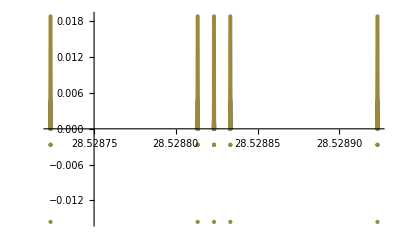

```mathematica
ListPlot[{evslo,evsmid,evshi},PlotRange->Full]
```

#### Testing Bisection Routine

```mathematica
BisectTest[F_,consts_,x0_,xf_,ϵ_]:=Module[{mid,val,lnegs,vam,mnegs,vah},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint is "<>ToString[mid]];
val=F[x0,consts];
lnegs=CountNegs[val];
vam=F[mid,consts];
mnegs=CountNegs[vam];
If[xf-x0>ϵ,
bisects=Append[bisects,{mid,{val[[1]],lnegs},{vam[[1]],mnegs}}];
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]), (*if there is a zero on the lower half*)
Return[BisectTest[F,consts,x0,mid,ϵ]];, (*bisect it*)
Return[BisectTest[F,consts,mid,xf,ϵ]]; (*otherwise try the upper half*)
];,
vah = F[xf,consts];
Return[{mid,lnegs,CountNegs[vah]}];
]
]
```

```mathematica
newins[[35]]
```

{2,2283.02,28.5221,28.5533}

```mathematica
bisects={};
```

```mathematica
BisectTest[Critical,{0.1,newins[[35,2]],newins[[35,2]]/0.1},newins[[35,3]],newins[[35,4]],10^(-6)]
```

Bisecting. Midpoint is 28.5377

Bisecting. Midpoint is 28.5299

Bisecting. Midpoint is 28.526

Bisecting. Midpoint is 28.5279

Bisecting. Midpoint is 28.5289

Bisecting. Midpoint is 28.5284

Bisecting. Midpoint is 28.5287

Bisecting. Midpoint is 28.5288

Bisecting. Midpoint is 28.5288

Bisecting. Midpoint is 28.5288

«6 more identical outputs»

{28.5288,0,1}

```mathematica
N[bisects,10]//TableForm
```

28.5377 | 4.06316×10^-8
0 | -5.49043×10^-8
1.
28.5299 | 4.06316×10^-8
0 | -6.42475×10^-9
1.
28.526 | 4.06316×10^-8
0 | 1.72791×10^-8
0
28.5279 | 1.72791×10^-8
0 | 5.47137×10^-9
0
28.5289 | 5.47137×10^-9
0 | -4.65605×10^-10
1.
28.5284 | 5.47137×10^-9
0 | 2.50565×10^-9
0
28.5287 | 2.50565×10^-9
0 | 1.02071×10^-9
0
28.5288 | 1.02071×10^-9
0 | 2.77728×10^-10
0
28.5288 | 2.77728×10^-10
0 | -9.38955×10^-11
1.
28.5288 | 2.77728×10^-10
0 | 9.19268×10^-11
0
28.5288 | 9.19268×10^-11
0 | -9.81714×10^-13
1.
28.5288 | 9.19268×10^-11
0 | 4.54731×10^-11
0
28.5288 | 4.54731×10^-11
0 | 2.22459×10^-11
0
28.5288 | 2.22459×10^-11
0 | 1.06321×10^-11
0
28.5288 | 1.06321×10^-11
0 | 4.82523×10^-12
0

```mathematica
Diffs=Table[bisects[[i+1,1]]-bisects[[i,1]],{i,1,Length[bisects]-1}]
```

{-0.0078125,-0.00390625,0.00195313,0.000976563,-0.000488281,0.000244141,0.00012207,0.0000610352,-0.0000305176,0.0000152588,-7.62939×10^-6,3.8147×10^-6,1.90735×10^-6,9.53674×10^-7}

```mathematica
?N
```

N[expr] gives the numerical value of expr. 
N[expr,n] attempts to give a result with n-digit precision.

### Data (evaluate me!)

```mathematica
lcs
```

{{1,{12.8273,1}},{1,{19.9501,2}},{1,{28.6423,1}},{1,{38.9044,2}},{1,{50.738,2}},{1,{64.1418,1}},{1,{79.116,2}},{1,{95.6605,2}},{1,{113.776,2}},{1,{133.462,2}},{1,{154.72,2}},{1,{177.547,2}},{1,{201.946,1}},{1,{227.915,2}},{1,{255.455,1}},{1,{284.566,2}},{1,{315.248,1}},{1,{347.501,2}},{1,{381.324,1}},{1,{416.718,2}},{1,{453.683,1}},{1,{492.219,1}},{1,{532.326,2}},{1,{574.003,2}},{1,{617.251,1}},{1,{662.07,2}},{1,{708.46,1}},{1,{756.421,2}},{1,{805.953,1}},{1,{857.055,1}},{1,{909.728,2}},{1,{963.973,2}},{2,{12.7556,1}},{2,{19.8574,0}},{2,{28.5288,0}},{2,{38.7702,0}},{2,{50.5817,1}},{2,{63.9635,0}},{2,{78.9157,0}},{2,{95.4383,1}},{2,{113.531,0}},{2,{133.195,0}},{2,{154.429,1}},{2,{177.234,1}},{2,{201.61,0,1}},{2,{227.556,1}},{2,{255.072,0}},{2,{284.16,1}},{2,{314.818,0}},{2,{347.047,1}},{2,{380.846,1}},{2,{416.216,1}},{2,{453.157,1}},{2,{491.669,1}},{2,{531.751,0}},{2,{573.404,1}},{2,{616.628,0}},{2,{661.423,0}},{2,{707.788,1}},{2,{755.724,0}},{2,{805.231,0}},{2,{856.308,1}},{2,{908.957,1}},{2,{963.176,0}}}

All leftover goodlcs have enough data for error bars. Yay error bars!

```mathematica
goodlcs=lcs;
```

Data for plotting/fitting will be in the form {{λc, error},{.....}}.

```mathematica
goodlcs=lcs={{1,{12.827343463897705,1}},{1,{19.95009756088257,2}},{1,{28.642311573028564,1}},{1,{38.904447078704834,2}},{1,{50.73803377151489,2}},{1,{64.141761302948,1}},{1,{79.11599397659302,2}},{1,{95.66045904159546,2}},{1,{113.77575731277466,2}},{1,{133.46212148666382,2}},{1,{154.7197699546814,2}},{1,{177.5473256111145,2}},{1,{201.94617700576782,1}},{1,{227.91507291793823,2}},{1,{255.45525884628296,1}},{1,{284.56644201278687,2}},{1,{315.2480025291443,1}},{1,{347.5005784034729,2}},{1,{381.32391595840454,1}},{1,{416.71833848953247,2}},{1,{453.68311834335327,1}},{1,{492.21898794174194,1}},{1,{532.3256268501282,2}},{1,{574.0033192634583,2}},{1,{617.251362323761,1}},{1,{662.0704569816589,2}},{1,{708.460343837738,1}},{1,{756.4213309288025,2}},{1,{805.9526534080505,1}},{1,{857.0550780296326,1}},{1,{909.7282948493958,2}},{1,{963.9725241661072,2}},{2,{12.755588054656982,1}},{2,{19.85741662979126,0}},{2,{28.528823375701904,0}},{2,{38.77021265029907,0}},{2,{50.58174180984497,1}},{2,{63.963539600372314,0}},{2,{78.91569757461548,0}},{2,{95.43831491470337,1}},{2,{113.53142023086548,0}},{2,{133.1950821876526,0}},{2,{154.4293065071106,1}},{2,{177.23412942886353,1}},{2,{201.60958051681519,0,1}},{2,{227.5556607246399,1}},{2,{255.07240915298462,0}},{2,{284.15981340408325,1}},{2,{314.81791067123413,0}},{2,{347.0466961860657,1}},{2,{380.84616899490356,1}},{2,{416.21636152267456,1}},{2,{453.1572594642639,1}},{2,{491.6688714027405,1}},{2,{531.751214504242,0}},{2,{573.4042925834656,1}},{2,{616.6280913352966,0}},{2,{661.4226317405701,0}},{2,{707.7879176139832,1}},{2,{755.7239384651184,0}},{2,{805.2307152748108,0}},{2,{856.3082346916199,1}},{2,{908.9565062522888,1}},{2,{963.1755290031433,0}}};
```

```mathematica
final=Table[{goodlcs[[i,2,1]],goodlcs[[i,2,1]]-goodlcs[[i+Length[lcs]/2,2,1]]},{i,1,Length[lcs]/2}]
```

{{12.8273,0.0717554},{19.9501,0.0926809},{28.6423,0.113488},{38.9044,0.134234},{50.738,0.156292},{64.1418,0.178222},{79.116,0.200296},{95.6605,0.222144},{113.776,0.244337},{133.462,0.267039},{154.72,0.290463},{177.547,0.313196},{201.946,0.336596},{227.915,0.359412},{255.455,0.38285},{284.566,0.406629},{315.248,0.430092},{347.501,0.453882},{381.324,0.477747},{416.718,0.501977},{453.683,0.525859},{492.219,0.550117},{532.326,0.574412},{574.003,0.599027},{617.251,0.623271},{662.07,0.647825},{708.46,0.672426},{756.421,0.697392},{805.953,0.721938},{857.055,0.746843},{909.728,0.771789},{963.973,0.796995}}

### Error Check

```mathematica
resfinal[[3]]
```

{14.165,15.1411}

```mathematica
newins[[1]]
```

{1,360.286,4.25358,4.75358}

```mathematica
2^9
```

512

```mathematica
ins=Table[{i,(2^(i-1)*10*resfinal[[3,1]]),resfinal[[4,1]]-0.5,resfinal[[4,2]]+0.5},{i,1,6}]
```

{{1,141.65,21.4736,23.4497},{2,283.301,21.4736,23.4497},{3,566.602,21.4736,23.4497},{4,1133.2,21.4736,23.4497},{5,2266.41,21.4736,23.4497},{6,4532.81,21.4736,23.4497}}

```mathematica
ins=ListRandomize[ins]
```

{{6,4532.81,21.4736,23.4497},{3,566.602,21.4736,23.4497},{5,2266.41,21.4736,23.4497},{2,283.301,21.4736,23.4497},{4,1133.2,21.4736,23.4497},{1,141.65,21.4736,23.4497}}

```mathematica
DistributeDefinitions[ins,Critical]
```

```mathematica
errlist=ParallelTable[Findlc[ins[[i]],i,10^(-6)],{i,1,Length[ins]}]
```

***Beginning to calculate the 1th lambda, part 6

***Beginning to calculate the 2th lambda, part 5

***Beginning to calculate the 2th lambda, part 2

***Beginning to calculate the 3th lambda, part 4

***Beginning to calculate the 3th lambda, part 1

Pass!

Bisecting. Midpoint is 22.4617

Pass!

Bisecting. Midpoint is 22.4617

Bisecting. Midpoint is 21.9677

Bisecting. Midpoint is 22.2147

Bisecting. Midpoint is 22.9557

Bisecting. Midpoint is 22.7087

Bisecting. Midpoint is 22.0912

Pass!

Bisecting. Midpoint is 22.4617

Bisecting. Midpoint is 22.1529

Bisecting. Midpoint is 22.8322

Bisecting. Midpoint is 22.1838

Bisecting. Midpoint is 22.7704

Bisecting. Midpoint is 22.1992

Bisecting. Midpoint is 22.8013

Bisecting. Midpoint is 22.2069

Bisecting. Midpoint is 22.7859

Bisecting. Midpoint is 21.9677

Bisecting. Midpoint is 22.2108

Bisecting. Midpoint is 22.7936

Bisecting. Midpoint is 22.2089

Pass!

Bisecting. Midpoint is 22.4617

Bisecting. Midpoint is 22.7897

Bisecting. Midpoint is 22.2098

Bisecting. Midpoint is 22.7878

Bisecting. Midpoint is 22.2103

Bisecting. Midpoint is 22.2106

Bisecting. Midpoint is 22.7868

Bisecting. Midpoint is 22.2147

Bisecting. Midpoint is 22.2107

Bisecting. Midpoint is 22.7864

Bisecting. Midpoint is 22.2107

Bisecting. Midpoint is 22.7866

Bisecting. Midpoint is 22.2108

Bisecting. Midpoint is 22.7867

Bisecting. Midpoint is 22.2108

Bisecting. Midpoint is 22.7868

Bisecting. Midpoint is 22.0912

Bisecting. Midpoint is 22.7867

Bisecting. Midpoint is 22.2108

Bisecting. Midpoint is 22.7867

Bisecting. Midpoint is 22.2108

Bisecting. Midpoint is 22.7867

Bisecting. Midpoint is 22.2108

Bisecting. Midpoint is 21.9677

Bisecting. Midpoint is 22.7867

Bisecting. Midpoint is 22.2108

Pass!

Bisecting. Midpoint is 22.4617

Bisecting. Midpoint is 22.2108

Bisecting. Midpoint is 22.1529

Bisecting. Midpoint is 22.7867

Bisecting. Midpoint is 22.7867

Bisecting. Midpoint is 22.7867

Bisecting. Midpoint is 22.122

Bisecting. Midpoint is 22.2147

Bisecting. Midpoint is 22.1375

Bisecting. Midpoint is 22.1298

Bisecting. Midpoint is 22.1259

Bisecting. Midpoint is 22.0912

Bisecting. Midpoint is 21.9677

Bisecting. Midpoint is 22.1278

Bisecting. Midpoint is 22.1288

Bisecting. Midpoint is 22.1529

Bisecting. Midpoint is 22.1293

Bisecting. Midpoint is 22.129

Bisecting. Midpoint is 22.122

Bisecting. Midpoint is 22.1289

Bisecting. Midpoint is 22.2147

Bisecting. Midpoint is 22.1288

Bisecting. Midpoint is 22.1375

Bisecting. Midpoint is 22.1288

Bisecting. Midpoint is 22.1288

Bisecting. Midpoint is 22.1288

Bisecting. Midpoint is 22.1298

Bisecting. Midpoint is 22.1288

Bisecting. Midpoint is 22.0912

Bisecting. Midpoint is 22.1288

Bisecting. Midpoint is 22.1259

Bisecting. Midpoint is 22.1288

Bisecting. Midpoint is 22.1288

Bisecting. Midpoint is 22.1278

Bisecting. Midpoint is 22.1529

Bisecting. Midpoint is 22.1269

Bisecting. Midpoint is 22.1273

Bisecting. Midpoint is 22.122

Bisecting. Midpoint is 22.1276

Bisecting. Midpoint is 22.1277

Bisecting. Midpoint is 22.1278

Bisecting. Midpoint is 22.1375

Bisecting. Midpoint is 22.1277

Bisecting. Midpoint is 22.1277

Bisecting. Midpoint is 22.1298

Bisecting. Midpoint is 22.1277

Bisecting. Midpoint is 22.1277

Bisecting. Midpoint is 22.1259

Bisecting. Midpoint is 22.1277

Bisecting. Midpoint is 22.1277

Bisecting. Midpoint is 22.1278

Bisecting. Midpoint is 22.1277

Bisecting. Midpoint is 22.1269

Bisecting. Midpoint is 22.1273

Bisecting. Midpoint is 22.1276

Bisecting. Midpoint is 22.1275

Bisecting. Midpoint is 22.1275

Bisecting. Midpoint is 22.1276

Bisecting. Midpoint is 22.1276

Bisecting. Midpoint is 22.1276

«4 more identical outputs»

***Beginning to calculate the 1th lambda, part 3

Pass!

Bisecting. Midpoint is 22.4617

Bisecting. Midpoint is 21.9677

Bisecting. Midpoint is 22.2147

Bisecting. Midpoint is 22.0912

Bisecting. Midpoint is 22.1529

Bisecting. Midpoint is 22.122

Bisecting. Midpoint is 22.1375

Bisecting. Midpoint is 22.1452

Bisecting. Midpoint is 22.1413

Bisecting. Midpoint is 22.1394

Bisecting. Midpoint is 22.1384

Bisecting. Midpoint is 22.138

Bisecting. Midpoint is 22.1377

Bisecting. Midpoint is 22.1378

Bisecting. Midpoint is 22.1379

Bisecting. Midpoint is 22.1379

Bisecting. Midpoint is 22.1379

«5 more identical outputs»

{{6,{22.1276,0,1}},{3,{22.1379,1,2}},{5,{22.1277,0,1}},{2,{22.2108,2,3}},{4,{22.1288,0,1}},{1,{22.7867,3,4}}}

```mathematica
test=Sort[%199]
```

{{1,{22.7867,3,4}},{2,{22.2108,2,3}},{3,{22.1379,1,2}},{4,{22.1288,0,1}},{5,{22.1277,0,1}},{6,{22.1276,0,1}}}

```mathematica
Results2=Table[{Round[2^(i-1)*10*resfinal[[3,1]]],test[[i,2,1]]},{i,1,Length[test]}]
```

{{142,22.7867},{283,22.2108},{567,22.1379},{1133,22.1288},{2266,22.1277},{4533,22.1276}}

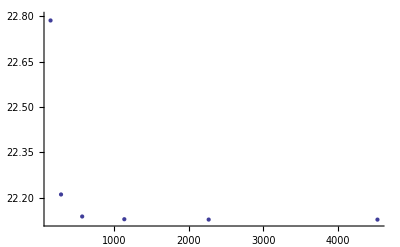

```mathematica
ListPlot[Results2, PlotRange->{22.12,22.80}]
```

```mathematica
ListRandomize[list_]:=Module[{order,res},
order=Table[{RandomReal[],i},{i,1,Length[list]}];
order = Sort[order];
res=Table[list[[order[[i,2]]]],{i,1,Length[list]}];
Return[res]
]
```

```mathematica
Table[Results2[[i,2]]>Results2[[i+1,2]],{i,1,Length[Results2]-1}]
```

{True,True,True,True,True}

```mathematica
Results
```

{{142,14.8466},{283,14.7435},{567,14.7304},{1133,14.7288},{2266,14.7286},{4533,14.7286},{9066,14.7286},{18131,14.7286},{36262,14.7286}}

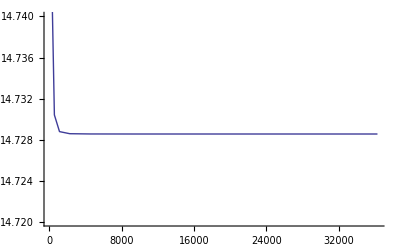

```mathematica
ListPlot[Results,PlotRange->{14.72,14.74},Joined->True]
```

```mathematica
Table[Results[[i,2]]>=Results[[i+1,2]],{i,1,Length[Results]-1}]
```

{True,True,True,True,True,True,True,True}

```mathematica
Table[Results[[i,2]]-Results[[i+1,2]],{i,1,Length[Results]-1}]
```

{0.103149,0.0130683,0.00162352,0.000203529,0.0000254412,3.76906×10^-6,0.,0.}

```mathematica
2^7*10*1000
```

1280000

### Plots!

Information on data collection --n=1 had rho_inf = 700, drho = 0.01. n = 2 and 3 had rho_inf = 2000, drho = 0.1. n = 3 through 14 had rho_inf = 40,000 and drho = 0.1.

```mathematica
Needs["ErrorBarPlots`"];
```

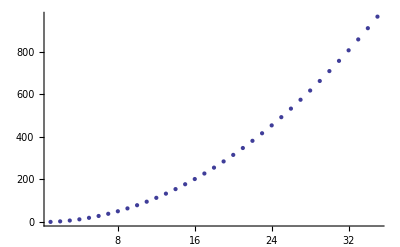

```mathematica
stuff = ErrorBarPlots`ErrorListPlot[final]
```

```mathematica
loglog=Table[{Log[2,N[i]],Log[2,final[[i,1]]]},{i,1,Length[final]}]
```

{{0.,-0.159566},{1.,1.72122},{1.58496,2.86549},{2.,3.68115},{2.32193,4.31832},{2.58496,4.84008},{2.80735,5.28186},{3.,5.665},{3.16993,6.00319},{3.32193,6.3059},{3.45943,6.57985},{3.58496,6.83005},{3.70044,7.06029},{3.80735,7.27351},{3.90689,7.47206},{4.,7.65783},{4.08746,7.83235},{4.16993,7.99693},{4.24793,8.15262},{4.32193,8.30034},{4.39232,8.44087},{4.45943,8.57487},{4.52356,8.70293},{4.58496,8.82554},{4.64386,8.94316},{4.70044,9.05617},{4.75489,9.16492},{4.80735,9.26971},{4.85798,9.37084},{4.90689,9.46854},{4.9542,9.56305},{5.,9.65455},{5.04439,9.74324},{5.08746,9.82929},{5.12928,9.91285}}

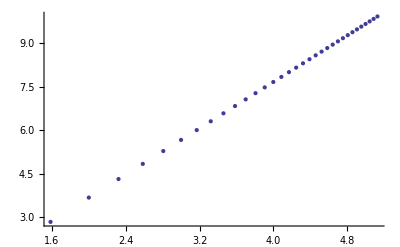

```mathematica
ListPlot[loglog]
```

```mathematica
fit=LinearModelFit[loglog,x,x]
```

FittedModel[-0.313547+1.99329 x]

```mathematica
fit["RSquared"]
```

0.999999

Linear wooooo!

```mathematica
f[x_] :=Normal[fit]
```

```mathematica
f[x]
```

-0.313547+1.99329 x

```mathematica
fit["ParameterErrors"]
```

{0.00166159,0.000404605}

```mathematica
Exp[-0.2789898192883946]
```

0.756548

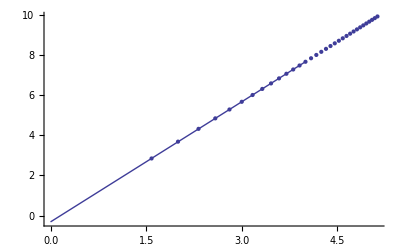

```mathematica
Show[ListPlot[loglog], Plot[f[x], {x, 0, 4}]]
```

### Weighted fit

final has data in the form {λc, Δλ} for n=1,2,3...

```mathematica
loglog=Table[{Log[N[i]],Log[final[[i,1]]],1/final[[i,1]]*final[[i,2]]},{i,1,Length[final]}]
```

{{0.,-0.110602,0.0308154},{0.693147,1.19306,0.0110979},{1.09861,1.9862,0.00814458},{1.38629,2.55158,0.00559394},{1.60944,2.99323,0.00464564},{1.79176,3.35489,0.00396226},{1.94591,3.66111,0.00345036},{2.07944,3.92668,0.00308037},{2.19722,4.1611,0.00277856},{2.30259,4.37092,0.00253168},{2.3979,4.56081,0.00232221},{2.48491,4.73423,0.00214753},{2.56495,4.89382,0.00200086},{2.63906,5.04162,0.00187735},{2.70805,5.17924,0.00176402},{2.77259,5.308,0.00166676},{2.83321,5.42897,0.00157696},{2.89037,5.54305,0.0014987},{2.94444,5.65097,0.00142894},{2.99573,5.75336,0.0013643},{3.04452,5.85077,0.00130613},{3.09104,5.94365,0.00125286},{3.13549,6.03241,0.0012046},{3.17805,6.1174,0.00115909},{3.21888,6.19892,0.00111763},{3.2581,6.27726,0.00107906},{3.29584,6.35264,0.00104359},{3.3322,6.42528,0.00100975},{3.3673,6.49537,0.000978484},{3.4012,6.56309,0.000949137},{3.43399,6.6286,0.000921963},{3.46574,6.69202,0.000895757},{3.49651,6.7535,0.000871406},{3.52636,6.81315,0.000848373},{3.55535,6.87106,0.000826782}}

```mathematica
weights=Table[1/(loglog[[i,3]]^2),{i,1,Length[loglog]}]
```

{1053.09,8119.26,15075.2,31956.9,46335.,63696.4,83998.3,105389.,129527.,156021.,185437.,216831.,249785.,283732.,321363.,359958.,402124.,445218.,489747.,537257.,586172.,637077.,689156.,744332.,800585.,858830.,918198.,980777.,1.04446×10^6,1.11005×10^6,1.17645×10^6,1.24629×10^6,1.31692×10^6,1.3894×10^6,1.46291×10^6}

```mathematica
Length[loglog]
```

35

Looking for form y = A + Bx.

```mathematica
Delta=Sum[weights[[i]],{i,Length[weights]}]*Sum[weights[[i]]*loglog[[i,1]]^2,{i,Length[loglog]}]-(Sum[weights[[i]]*loglog[[i,1]],{i,Length[loglog]}])^2;
```

```mathematica
x[i_]:=loglog[[i,1]];
y[i_]:=loglog[[i,2]];
w[i_]:=weights[[i]]; (*to make reading below easier*)
```

```mathematica
A=(Sum[w
[i]*x[i]^2,{i,Length[loglog]}]*Sum[w[i]*y[i],{i,Length[loglog]}]-Sum[w[i]*x[i],{i,Length[loglog]}]*Sum[w[i]*x[i]*y[i],{i,Length[loglog]}])/Delta
```

-0.22149

There’s the intercept.

```mathematica
B=(Sum[w
[i],{i,Length[loglog]}]*Sum[w[i]*x[i]*y[i],{i,Length[loglog]}]-Sum[w[i]*x[i],{i,Length[loglog]}]*Sum[w[i]*y[i],{i,Length[loglog]}])/Delta
```

1.9947

And the slope! Uncertainties:

```mathematica
σA=Sqrt[Sum[w[i]*x[i]^2,{i,Length[loglog]}]/Delta]
```

0.00206866

```mathematica
σB=Sqrt[Sum[w[i],{i,Length[loglog]}]/Delta]
```

0.000640333

The fit still, at this point, appears not quite quadratic.

```mathematica
F[x_]:=A+B*x
```

```mathematica
fitvals=Table[F[loglog[[i,1]]],{i,1,Length[loglog]}];
```

```mathematica
Res=Table[fitvals[[i]]-loglog[[i,2]],{i,1,Length[loglog]}];
```

```mathematica
Table[Abs[Res[[i]]]<loglog[[i,3]],{i,1,Length[loglog]}]
```

{False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
CalloohCallay[]
```

```mathematica
Res
```

{-0.0232246,0.00903102,0.0151718,0.00653085,0.00819484,0.00876176,0.00878914,0.0085085,0.00808801,0.00758818,0.00705077,0.00649169,0.00592418,0.00535652,0.00480289,0.00425745,0.00372842,0.00321074,0.00270652,0.00221795,0.00174259,0.00128097,0.000831857,0.000396542,-0.0000272068,-0.000439149,-0.000840298,-0.00122992,-0.00160969,-0.00197964,-0.00234061,-0.00269198,-0.00303517,-0.00337013,-0.00369745}

```mathematica
fitvals
```

{-0.196039,1.18104,1.98657,2.55811,3.00143,3.36365,3.6699,3.93518,4.16918,4.3785,4.56786,4.74072,4.89974,5.04697,5.18404,5.31226,5.4327,5.54626,5.65367,5.75558,5.85251,5.94493,6.03324,6.1178,6.1989,6.27682,6.35179,6.42405,6.49376,6.56111,6.62626,6.68933,6.75047,6.80978,6.86737}

```mathematica
Table[loglog[[i,2]],{i,1,14}]
```

{-0.172814,1.172,1.9714,2.55158,2.99323,3.35489,3.66111,3.92668,4.1611,4.37092,4.56081,4.73423,4.89382,5.04162}

```mathematica
Length[final]
```

33

```mathematica
test = Table[final[[i, 1]], {i, 1, 33}]
```

{0.841294,3.22846,7.18073,12.8273,19.9501,28.6423,38.9044,50.738,64.1418,79.116,95.6605,113.776,133.462,154.72,177.547,201.946,227.915,255.455,284.566,315.248,347.501,381.324,416.718,453.683,492.219,532.326,574.003,617.251,662.07,708.46,756.421,805.953,857.055}

```mathematica
FindFit[test, a*x^2, {a}, x]
```

{a→0.787406}

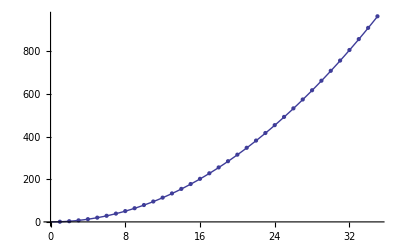

```mathematica
Show[Plot[.7863*x^2, {x, 0, 35}], stuff]
```